Axes::axes: {2.72905, {Thickness[Large]}} is not a valid axis specification.

Axes::axes: {-29.8645, {Thickness[Large]}} is not a valid axis specification.

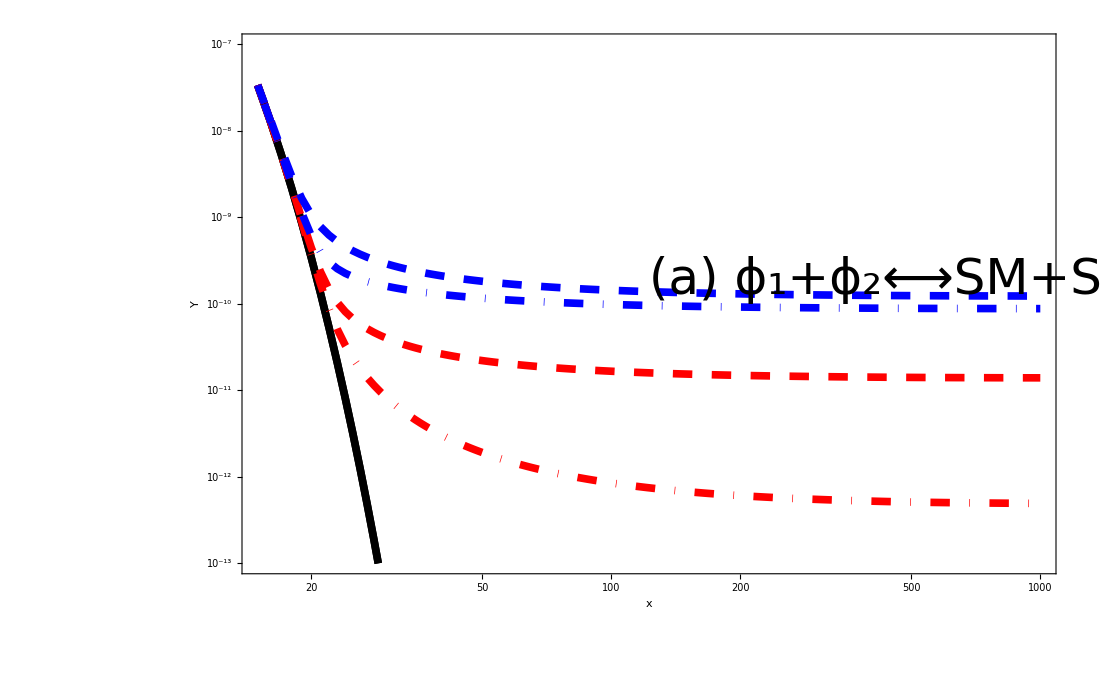

Axes::axes: {2.72905, {Thickness[Large]}} is not a valid axis specification.

Axes::axes: {-29.8645, {Thickness[Large]}} is not a valid axis specification.

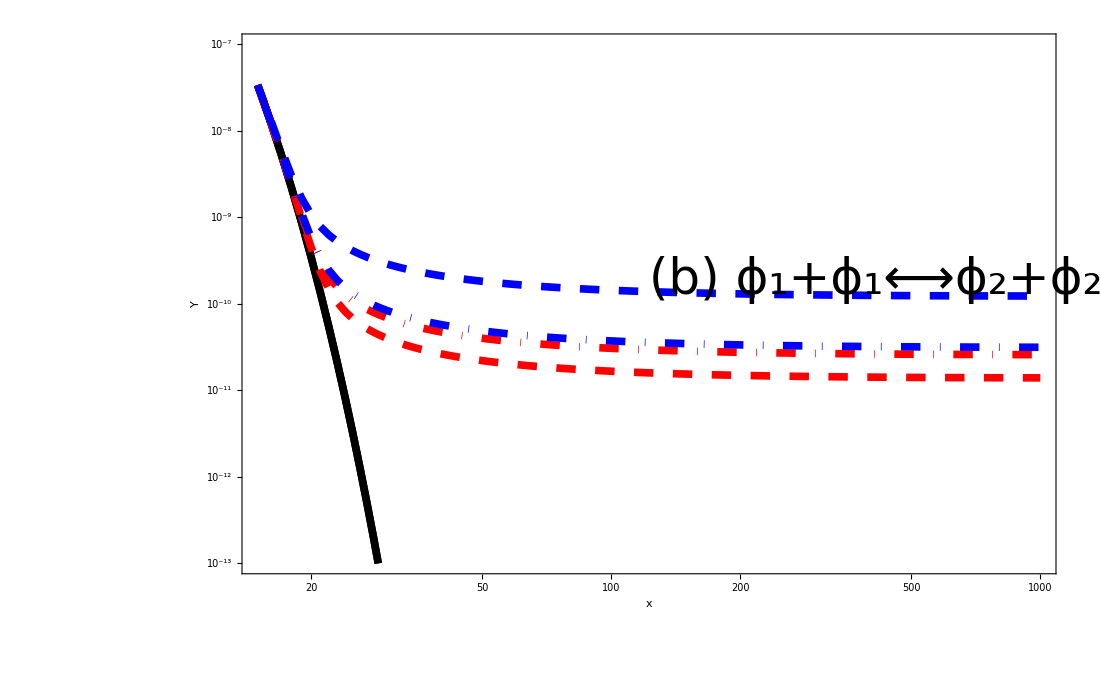

```mathematica
getTicks[pl_]:=Block[{},
tx=Map[MapAt[3#&,#,3]&,Ticks/.AbsoluteOptions[pl,Ticks],{2}];
tx=Map[MapAt[{GrayLevel[0.],AbsoluteThickness[3]}&,#,4]&,tx,{2}];
tx=Map[MapAt[Rationalize[#,10^-15]&,#,2]&,tx,{2}];
{tx[[1]],tx[[2]],None,None}
]

file= Import["C:\\Users\\AlexandrePoulin\\Documents\\relic\\freezeout_v2.5\\outputFiles\\waveTest\\outputOmegaBase.txt","Data"];
file2= Import["C:\\Users\\AlexandrePoulin\\Documents\\relic\\freezeout_v2.5\\outputFiles\\waveTest\\outputOmegaCo.txt","Data"];
file3= Import["C:\\Users\\AlexandrePoulin\\Documents\\relic\\freezeout_v2.5\\outputFiles\\waveTest\\outputOmegaConv.txt","Data"];

numDM = 2;

thick=Thickness[0.005];
dashed=Dashing[Large];
dotdash=Dashing[{0,Large,Large,Large}];
plotStyle = {{Black,thick},{Black,thick},{Red,thick,dashed},{Blue,thick,dashed}};
plotStyle2 = {{Red,thick,dotdash},{Blue,thick,dotdash}};

massScale=100;
(*should get 0.110 and 0.0128 for omegas *)

plotDataeq = Table[Table[{massScale/file[[a]][[1]],file[[a]][[2*b]]},{a,Length[file]}],{b,1,numDM}];
plotData= Table[Table[{massScale/file[[a]][[1]],file[[a]][[2*b+1]]},{a,Length[file]}],{b,1,numDM}];

plotDataeq2 = Table[Table[{massScale/file2[[a]][[1]],file2[[a]][[2*b]]},{a,Length[file2]}],{b,1,numDM}];
plotData2= Table[Table[{massScale/file2[[a]][[1]],file2[[a]][[2*b+1]]},{a,Length[file2]}],{b,1,numDM}];

plotDataeq3 = Table[Table[{massScale/file3[[a]][[1]],file3[[a]][[2*b]]},{a,Length[file3]}],{b,1,numDM}];
plotData3= Table[Table[{massScale/file3[[a]][[1]],file3[[a]][[2*b+1]]},{a,Length[file3]}],{b,1,numDM}];


plot1=ListLogLogPlot[Join[plotDataeq,plotData],PlotRange->{{15,1000},{10^(-13),10^-7}},Joined->True,PlotStyle->plotStyle(*,PlotLegends->{"Y_eq","Y"}*),BaseStyle->{FontSize->20},ImageSize->{1100,750},AxesStyle->Thick];
plot2=ListLogLogPlot[plotData2,PlotRange->{{10,1000},{10^(-13),10^-7}},Joined->True,PlotStyle->plotStyle2(*,PlotLegends->{"Y_eq","Y"}*),BaseStyle->{FontSize->20},ImageSize->{1100,750},AxesStyle->Thick];
plot3=ListLogLogPlot[plotData3,PlotRange->{{10,1000},{10^(-13),10^-7}},Joined->True,PlotStyle->plotStyle2(*,PlotLegends->{"Y_eq","Y"}*),BaseStyle->{FontSize->20},ImageSize->{1100,750},AxesStyle->Thick];


Show[{plot1,plot2},FrameStyle->Thickness[0.005],FrameTicks->getTicks[plot1],BaseStyle->{FontSize->50},Frame-> True,FrameLabel->{"x"," Y"},LabelStyle->Black,Epilog->{Text[Style["(a) ϕ_1+ϕ_2⟷SM+SM",50],Scaled[{0.5,0.5}],{-0.75,-7}]}]
Show[{plot1,plot3},FrameStyle->Thickness[0.005],FrameTicks->getTicks[plot1],BaseStyle->{FontSize->50},Frame-> True,FrameLabel->{"x"," Y"},LabelStyle->Black,Epilog->{Text[Style["(b) ϕ_1+ϕ_1⟷ϕ_2+ϕ_2",50],Scaled[{0.5,0.5}],{-0.71,-7}]}]
```

Axes::axes: {2.72905, {Thickness[Large]}} is not a valid axis specification.

Axes::axes: {-34.4697, {Thickness[Large]}} is not a valid axis specification.

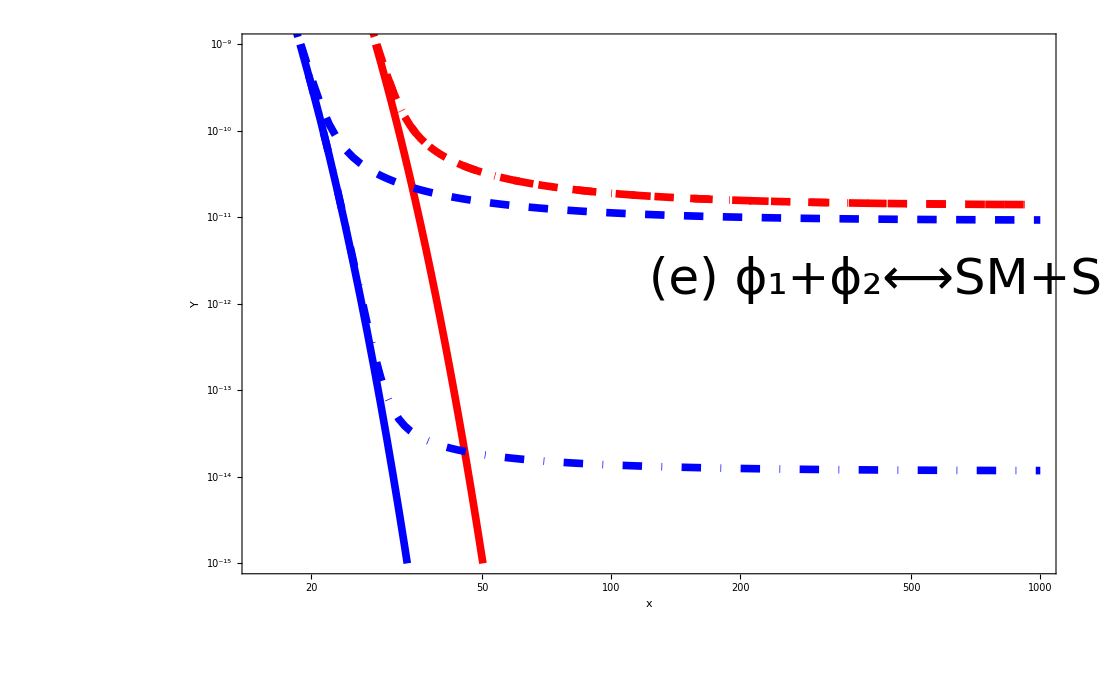

Axes::axes: {2.72905, {Thickness[Large]}} is not a valid axis specification.

Axes::axes: {-34.4697, {Thickness[Large]}} is not a valid axis specification.

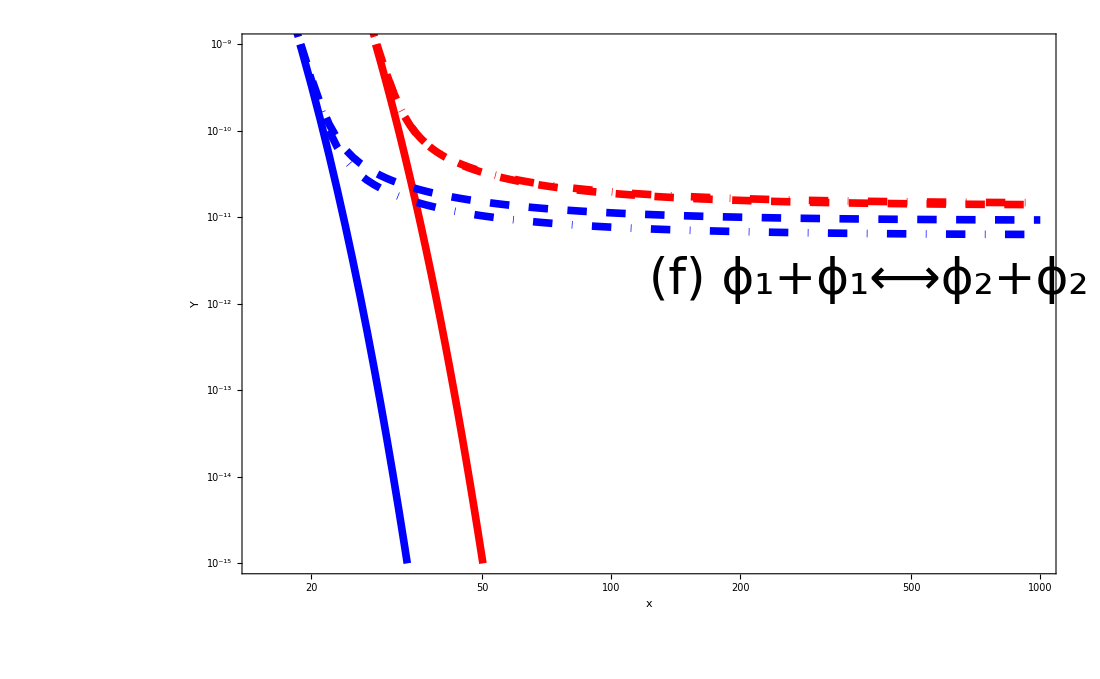

```mathematica
file= Import["C:\\Users\\AlexandrePoulin\\Documents\\relic\\freezeout_v2.5\\outputFiles\\waveTest\\outputOmegaDiffBase.txt","Data"];
file2= Import["C:\\Users\\AlexandrePoulin\\Documents\\relic\\freezeout_v2.5\\outputFiles\\waveTest\\outputOmegaDiffCo.txt","Data"];
file3= Import["C:\\Users\\AlexandrePoulin\\Documents\\relic\\freezeout_v2.5\\outputFiles\\waveTest\\outputOmegaDiffConv.txt","Data"];

numDM = 2;

thick=Thickness[0.005];
dashed=Dashing[Large];
dotdash=Dashing[{0,Large,Large,Large}];
plotStyle = {{Red,thick},{Blue,thick},{Red,thick,dashed},{Blue,thick,dashed}};
plotStyle2 = {{Blue,thick,dotdash},{Red,thick,dotdash}};
plotStyle3 = {{Red,thick,dotdash},{Blue,thick,dotdash}};

massScale=150;
(*should get 0.110 and 0.0128 for omegas *)

plotDataeq = Table[Table[{massScale/file[[a]][[1]],file[[a]][[2*b]]},{a,Length[file]}],{b,1,numDM}];
plotData= Table[Table[{massScale/file[[a]][[1]],file[[a]][[2*b+1]]},{a,Length[file]}],{b,1,numDM}];

plotDataeq2 = Table[Table[{massScale/file2[[a]][[1]],file2[[a]][[2*b]]},{a,Length[file2]}],{b,1,numDM}];
plotData2= Table[Table[{massScale/file2[[a]][[1]],file2[[a]][[2*b+1]]},{a,Length[file2]}],{b,1,numDM}];

plotDataeq3 = Table[Table[{massScale/file3[[a]][[1]],file3[[a]][[2*b]]},{a,Length[file3]}],{b,1,numDM}];
plotData3= Table[Table[{massScale/file3[[a]][[1]],file3[[a]][[2*b+1]]},{a,Length[file3]}],{b,1,numDM}];


plot1=ListLogLogPlot[Join[plotDataeq,plotData],PlotRange->{{15,1000},{10^(-15),10^-9}},Joined->True,PlotStyle->plotStyle(*,PlotLegends->{"Y_eq","Y"}*),BaseStyle->{FontSize->20},ImageSize->{1100,750},AxesStyle->Thick];
plot2=ListLogLogPlot[plotData2,PlotRange->{{10,1000},{10^(-15),10^-7}},Joined->True,PlotStyle->plotStyle3(*,PlotLegends->{"Y_eq","Y"}*),BaseStyle->{FontSize->20},ImageSize->{1100,750},AxesStyle->Thick];
plot3=ListLogLogPlot[plotData3,PlotRange->{{10,1000},{10^(-13),10^-7}},Joined->True,PlotStyle->plotStyle2(*,PlotLegends->{"Y_eq","Y"}*),BaseStyle->{FontSize->20},ImageSize->{1100,750},AxesStyle->Thick];
Show[{plot1,plot2},FrameStyle->Thickness[0.005],FrameTicks->getTicks[plot1],BaseStyle->{FontSize->50},Frame-> True,FrameLabel->{"x"," Y"},LabelStyle->Black,Epilog->{Text[Style["(e) ϕ_1+ϕ_2⟷SM+SM",50],Scaled[{0.5,0.5}],{-0.75,-7}]}]
Show[{plot1,plot3},FrameStyle->Thickness[0.005],FrameTicks->getTicks[plot1],BaseStyle->{FontSize->50},Frame-> True,FrameLabel->{"x"," Y"},LabelStyle->Black,Epilog->{Text[Style["(f) ϕ_1+ϕ_1⟷ϕ_2+ϕ_2",50],Scaled[{0.5,0.5}],{-0.75,-7}]}]
```

Axes::axes: {2.72905, {Thickness[Large]}} is not a valid axis specification.

Axes::axes: {-29.8645, {Thickness[Large]}} is not a valid axis specification.

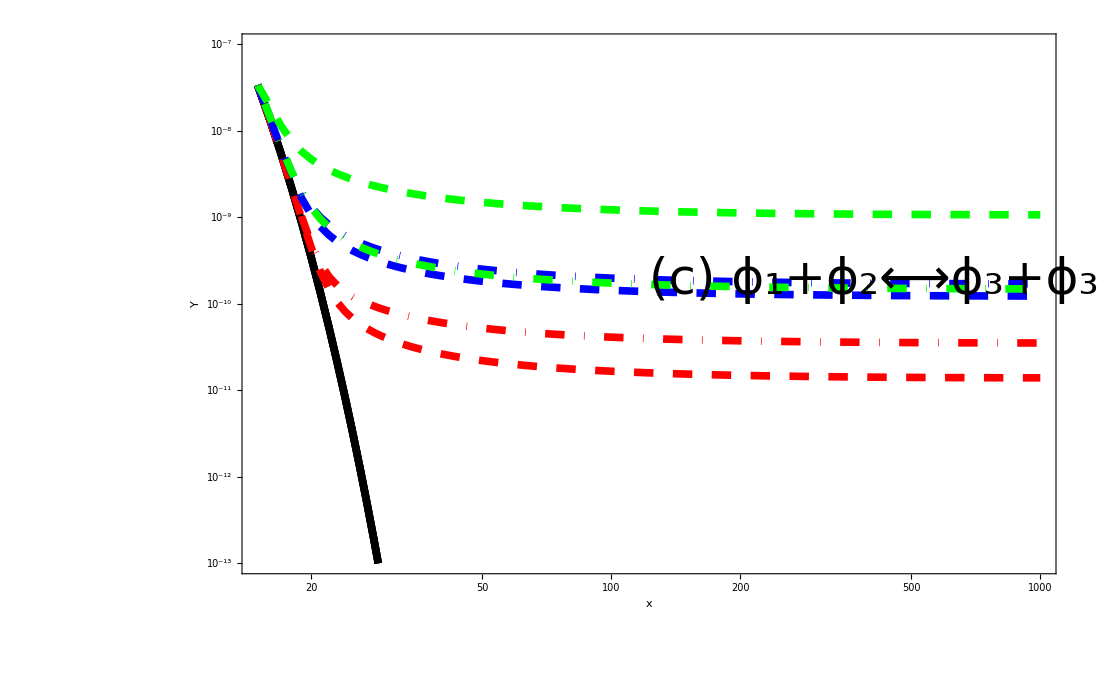

Axes::axes: {2.72905, {Thickness[Large]}} is not a valid axis specification.

Axes::axes: {-29.8645, {Thickness[Large]}} is not a valid axis specification.

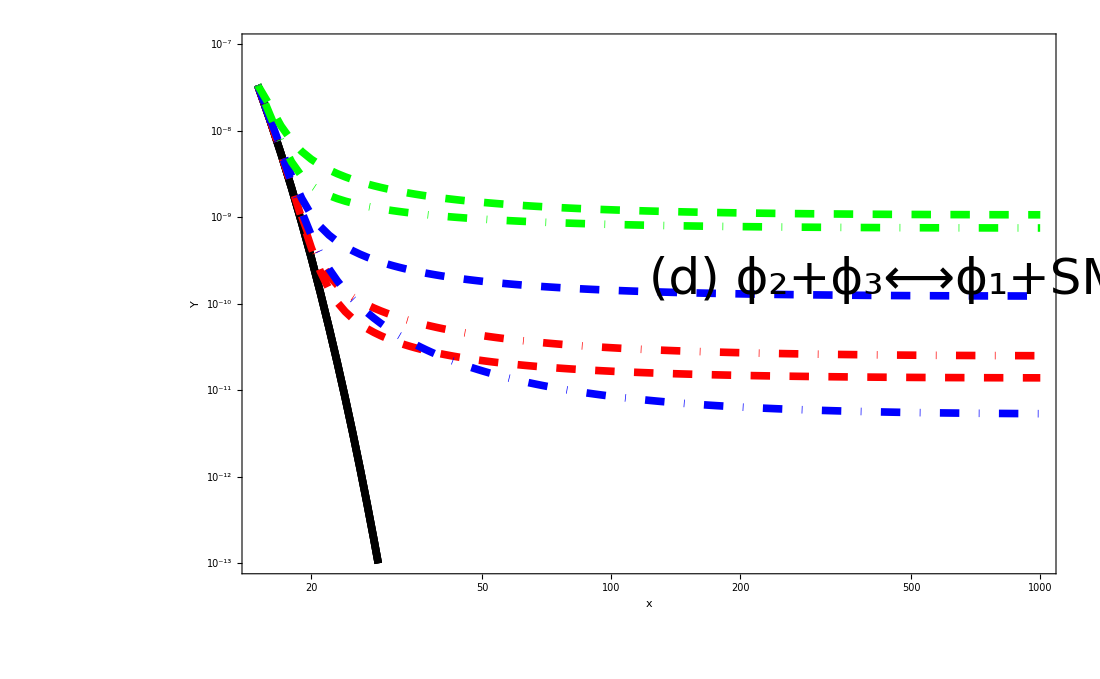

```mathematica
file= Import["C:\\Users\\AlexandrePoulin\\Documents\\relic\\freezeout_v2.5\\outputFiles\\waveTest\\outputOmegaBase3.txt","Data"];
file2= Import["C:\\Users\\AlexandrePoulin\\Documents\\relic\\freezeout_v2.5\\outputFiles\\waveTest\\outputOmega2to1.txt","Data"];
file3= Import["C:\\Users\\AlexandrePoulin\\Documents\\relic\\freezeout_v2.5\\outputFiles\\waveTest\\outputOmega1234.txt","Data"];


numDM = 3;

thick=Thickness[0.005];
dashed=Dashing[Large];
dotdash=Dashing[{0,Large,Large,Large}];
plotStyle = {{Black,thick},{Black,thick},{Black,thick},{Red,thick,dashed},{Blue,thick,dashed},{Green,thick,dashed}};
plotStyle2 = {{Red,thick,dotdash},{Blue,thick,dotdash},{Green,thick,dotdash}};

massScale=100;
(*should get 0.110 and 0.0128 for omegas *)

plotDataeq = Table[Table[{massScale/file[[a]][[1]],file[[a]][[2*b]]},{a,Length[file]}],{b,1,numDM}];
plotData= Table[Table[{massScale/file[[a]][[1]],file[[a]][[2*b+1]]},{a,Length[file]}],{b,1,numDM}];

plotDataeq2 = Table[Table[{massScale/file2[[a]][[1]],file2[[a]][[2*b]]},{a,Length[file2]}],{b,1,numDM}];
plotData2= Table[Table[{massScale/file2[[a]][[1]],file2[[a]][[2*b+1]]},{a,Length[file2]}],{b,1,numDM}];

plotDataeq3 = Table[Table[{massScale/file3[[a]][[1]],file3[[a]][[2*b]]},{a,Length[file3]}],{b,1,numDM}];
plotData3= Table[Table[{massScale/file3[[a]][[1]],file3[[a]][[2*b+1]]},{a,Length[file3]}],{b,1,numDM}];




plot1=ListLogLogPlot[Join[plotDataeq,plotData],PlotRange->{{15,1000},{10^(-13),10^-7}},Joined->True,PlotStyle->plotStyle(*,PlotLegends->{"Y_eq","Y"}*),BaseStyle->{FontSize->20},ImageSize->{1100,750},AxesStyle->Thick];
plot2=ListLogLogPlot[plotData2,PlotRange->{{10,1000},{10^(-13),10^-7}},Joined->True,PlotStyle->plotStyle2(*,PlotLegends->{"Y_eq","Y"}*),BaseStyle->{FontSize->20},ImageSize->{1100,750},AxesStyle->Thick];
plot3=ListLogLogPlot[plotData3,PlotRange->{{10,1000},{10^(-13),10^-7}},Joined->True,PlotStyle->plotStyle2(*,PlotLegends->{"Y_eq","Y"}*),BaseStyle->{FontSize->20},ImageSize->{1100,750},AxesStyle->Thick];
Show[{plot1,plot2},FrameStyle->Thickness[0.005],FrameTicks->getTicks[plot1],BaseStyle->{FontSize->50},Frame-> True,FrameLabel->{"x"," Y"},LabelStyle->Black,Epilog->{Text[Style["(c) ϕ_1+ϕ_2⟷ϕ_3+ϕ_3",50],Scaled[{0.5,0.5}],{-0.75,-7}]}]
Show[{plot1,plot3},FrameStyle->Thickness[0.005],FrameTicks->getTicks[plot1],BaseStyle->{FontSize->50},Frame-> True,FrameLabel->{"x"," Y"},LabelStyle->Black,Epilog->{Text[Style["(d) ϕ_2+ϕ_3⟷ϕ_1+SM",50],Scaled[{0.5,0.5}],{-0.75,-7}]}]
```

Axes::axes: {2.72905, {Thickness[Large]}} is not a valid axis specification.

Axes::axes: {-45.902, {Thickness[Large]}} is not a valid axis specification.

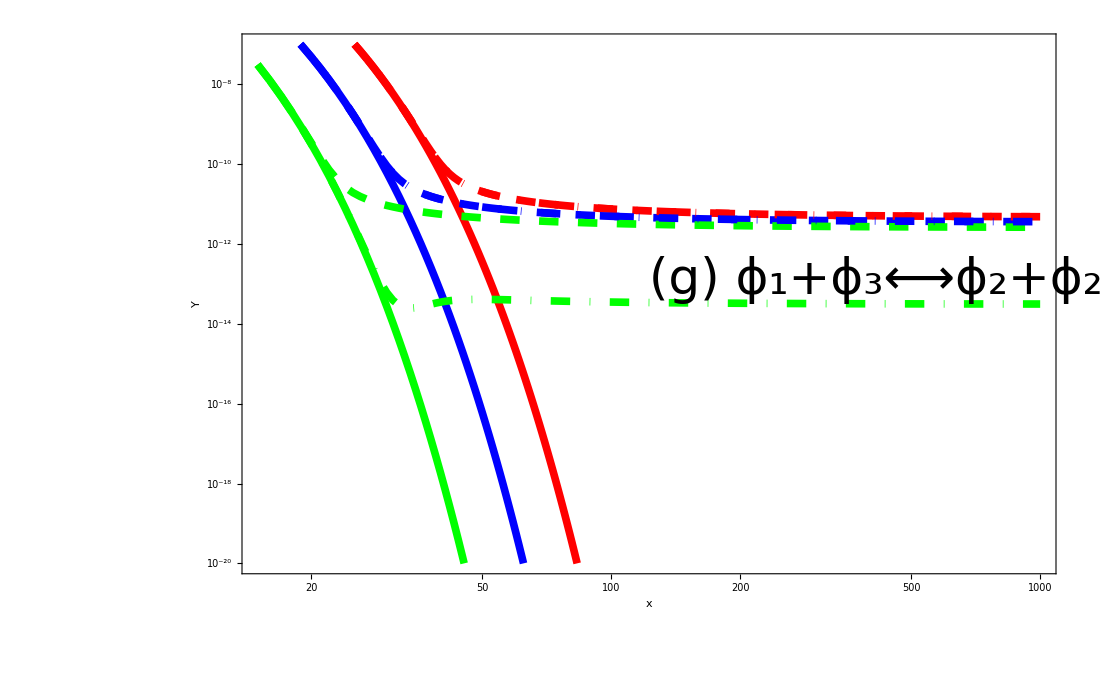

Axes::axes: {2.72905, {Thickness[Large]}} is not a valid axis specification.

Axes::axes: {-45.902, {Thickness[Large]}} is not a valid axis specification.

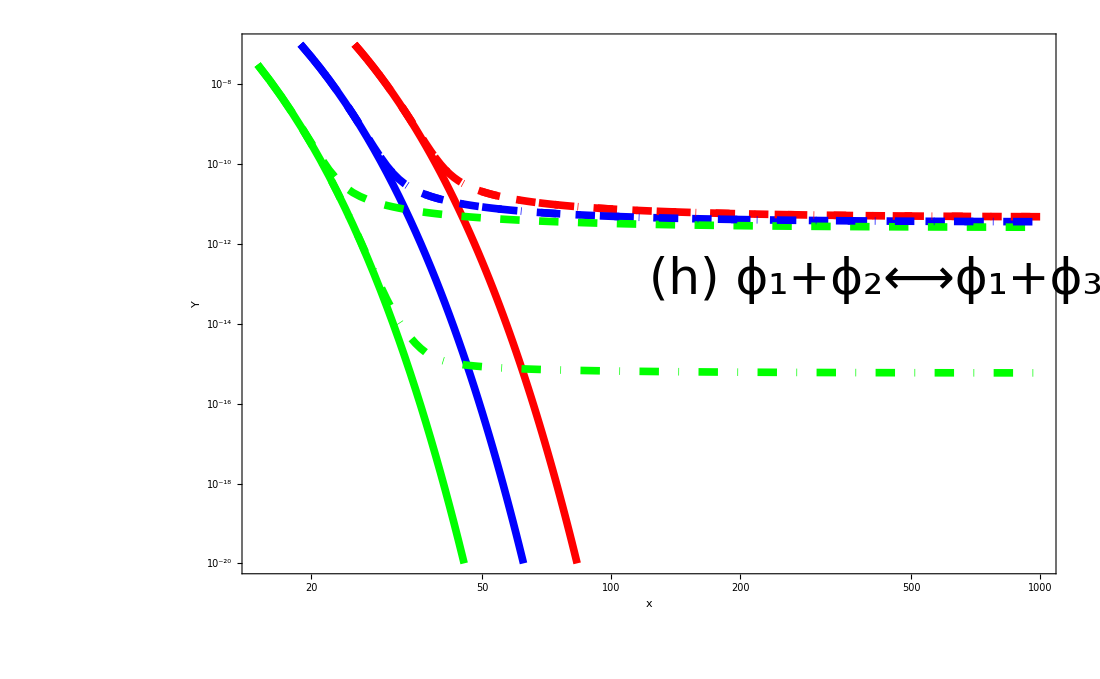

```mathematica
file= Import["C:\\Users\\AlexandrePoulin\\Documents\\relic\\freezeout_v2.5\\outputFiles\\waveTest\\outputOmegaBase3Diff.txt","Data"];
file2= Import["C:\\Users\\AlexandrePoulin\\Documents\\relic\\freezeout_v2.5\\outputFiles\\waveTest\\outputOmegaOneWay.txt","Data"];
file3= Import["C:\\Users\\AlexandrePoulin\\Documents\\relic\\freezeout_v2.5\\outputFiles\\waveTest\\outputOmegaOneWay2.txt","Data"];


numDM = 3;

thick=Thickness[0.005];
dashed=Dashing[Large];
dotdash=Dashing[{0,Large,Large,Large}];
plotStyle = {{Red,thick},{Blue,thick},{Green,thick},{Red,thick,dashed},{Blue,thick,dashed},{Green,thick,dashed}};
plotStyle2 = {{Red,thick,dotdash},{Blue,thick,dotdash},{Green,thick,dotdash}};
plotStyle3 = {{Blue,thick,dotdash},{Red,thick,dotdash},{Green,thick,dotdash}};

massScale=550;
(*should get 0.110 and 0.0128 for omegas *)

plotDataeq = Table[Table[{massScale/file[[a]][[1]],file[[a]][[2*b]]},{a,Length[file]}],{b,1,numDM}];
plotData= Table[Table[{massScale/file[[a]][[1]],file[[a]][[2*b+1]]},{a,Length[file]}],{b,1,numDM}];

plotDataeq2 = Table[Table[{massScale/file2[[a]][[1]],file2[[a]][[2*b]]},{a,Length[file2]}],{b,1,numDM}];
plotData2= Table[Table[{massScale/file2[[a]][[1]],file2[[a]][[2*b+1]]},{a,Length[file2]}],{b,1,numDM}];

plotDataeq3 = Table[Table[{massScale/file3[[a]][[1]],file3[[a]][[2*b]]},{a,Length[file3]}],{b,1,numDM}];
plotData3= Table[Table[{massScale/file3[[a]][[1]],file3[[a]][[2*b+1]]},{a,Length[file3]}],{b,1,numDM}];




plot1=ListLogLogPlot[Join[plotDataeq,plotData],PlotRange->{{15,1000},{10^(-20),10^-7}},Joined->True,PlotStyle->plotStyle(*,PlotLegends->{"Y_eq","Y"}*),BaseStyle->{FontSize->20},ImageSize->{1100,750},AxesStyle->Thick];
plot2=ListLogLogPlot[plotData2,PlotRange->{{10,1000},{10^(-17),10^-7}},Joined->True,PlotStyle->plotStyle2(*,PlotLegends->{"Y_eq","Y"}*),BaseStyle->{FontSize->20},ImageSize->{1100,750},AxesStyle->Thick];
plot3=ListLogLogPlot[plotData3,PlotRange->{{10,1000},{10^(-20),10^-7}},Joined->True,PlotStyle->plotStyle2(*,PlotLegends->{"Y_eq","Y"}*),BaseStyle->{FontSize->20},ImageSize->{1100,750},AxesStyle->Thick];

Show[{plot1,plot2},FrameStyle->Thickness[0.005],FrameTicks->getTicks[plot1],BaseStyle->{FontSize->50},Frame-> True,FrameLabel->{"x"," Y"},LabelStyle->Black,Epilog->{Text[Style["(g) ϕ_1+ϕ_3⟷ϕ_2+ϕ_2",50],Scaled[{0.5,0.5}],{-0.75,-7}]}]
Show[{plot1,plot3},FrameStyle->Thickness[0.005],FrameTicks->getTicks[plot1],BaseStyle->{FontSize->50},Frame-> True,FrameLabel->{"x"," Y"},LabelStyle->Black,Epilog->{Text[Style["(h) ϕ_1+ϕ_2⟷ϕ_1+ϕ_3",50],Scaled[{0.5,0.5}],{-0.75,-7}]}]
```

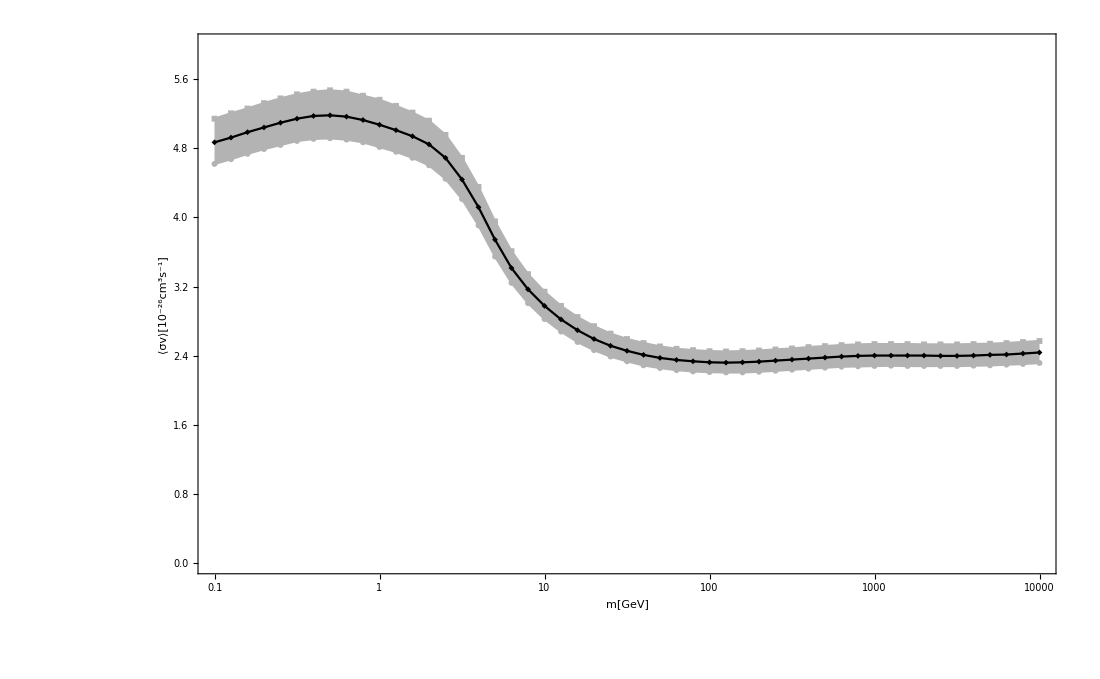

```mathematica
file3= Import["C:\\Users\\AlexandrePoulin\\Documents\\relic\\freezeout_v2.2\\outputFiles\\outputOmegaData.txt","Data"];
file4= Import["C:\\Users\\AlexandrePoulin\\Documents\\relic\\freezeout_v2.2\\outputFiles\\outputOmegaDataMerr.txt","Data"];
file5= Import["C:\\Users\\AlexandrePoulin\\Documents\\relic\\freezeout_v2.2\\outputFiles\\outputOmegaDataPerr.txt","Data"];
(*file6= Import["C:\\Users\\AlexandrePoulin\\Documents\\relic\\freezeout_v2.2\\outputFiles\\outputOmegaDataTest.txt","Data"];*)
plotDataOmegaMid= Table[{file3[[a]][[1]],file3[[a]][[2]]*10^(26)},{a,Length[file3]}];
plotDataOmegaMerr= Table[{file4[[a]][[1]],file4[[a]][[2]]*10^(26)},{a,Length[file4]}];
plotDataOmegaPerr= Table[{file5[[a]][[1]],file5[[a]][[2]]*10^(26)},{a,Length[file5]}];
(*plotDataOmegaTest= Table[{file6[[a]][[1]],file6[[a]][[2]]*10^(26)},{a,Length[file6]}];*)
p=ListLogLinearPlot[{plotDataOmegaPerr,plotDataOmegaMerr,plotDataOmegaMid},PlotRange->{{10^-1,10^4},{0,6}}(*PlotRange->{{4,4.5},{0,6}}*),BaseStyle->{FontSize->20},PlotMarkers->{Automatic,6},ImageSize->{1100,750},AxesStyle->Thick,TicksStyle->Thick,PlotStyle->{RGBColor[0.7,0.7,0.7],RGBColor[0.7,0.7,0.7],Black,Red},Filling->{1->{2}},FillingStyle->{RGBColor[0.7,0.7,0.7]},Joined->True];
Show[p,FrameStyle->Thick,FrameTicksStyle->Thick,BaseStyle->{FontSize->40},Frame-> True,FrameLabel->{"m[GeV]","⟨σv⟩[10^-26cm^3s^-1]"}]
```

```mathematica
con = 3.336*10^25;
4.8*10^-26*con
```

1.60128

```mathematica
45.0/(4*Pi^4)*Sqrt[Pi/2]
```

0.144748

```mathematica
Integrate[x^2*Exp[-x*a],{x,1,Infinity}]
```

ConditionalExpression[((2+a (2+a)) ⅇ^-a)/a^3,Re[a]>0]

```mathematica
Sqrt[Pi]/(Gamma[3/2]*4)
```

1/2

```mathematica
Integrate[Sqrt[(x^2-1)]*x,x]*D[Exp[-x*a]]
```

1/3 ⅇ^(-a x) (-1+x^2)^(3/2)

```mathematica
massScale/5
```

13.44

```mathematica
massScale/(1.0+9988995*0.0001)
```

0.0672068

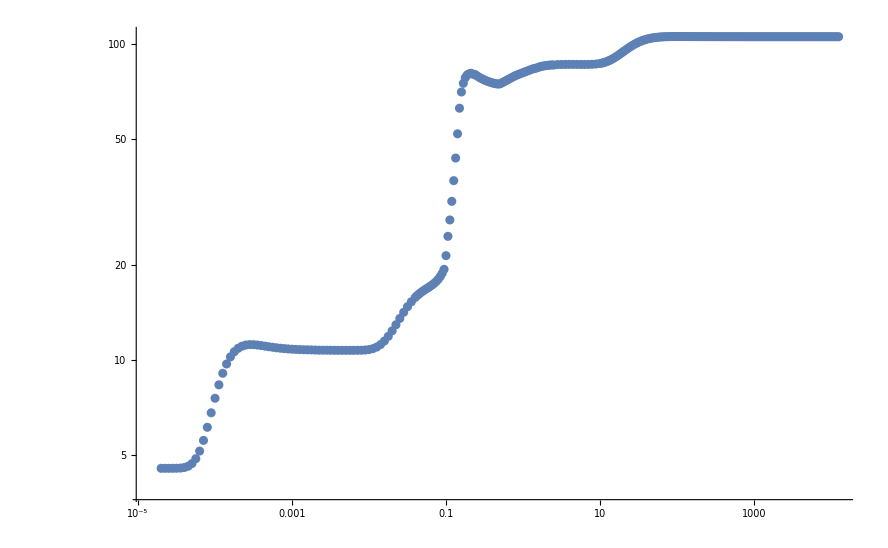

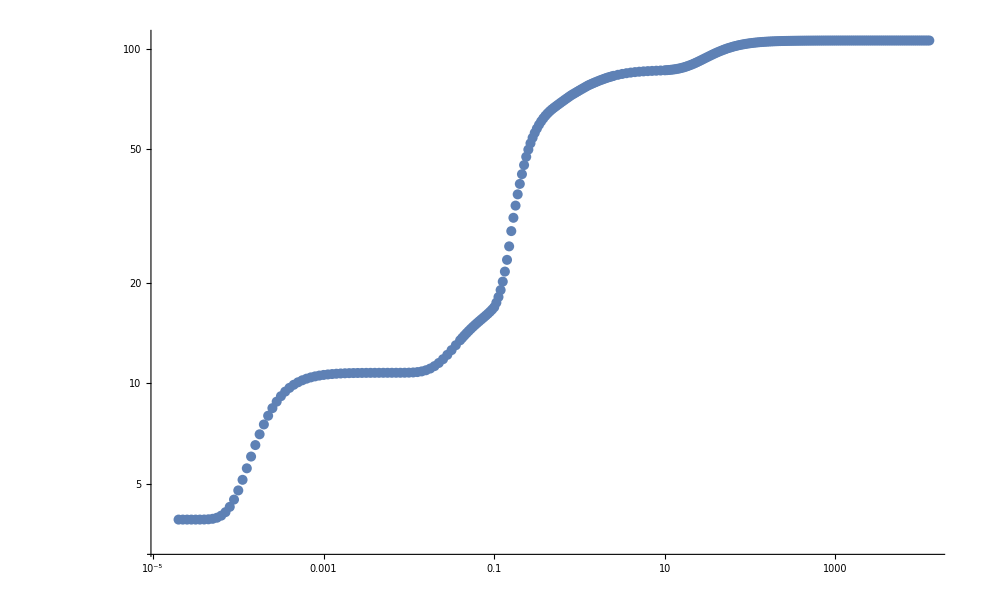

```mathematica
file6= Import["C:\\Users\\AlexandrePoulin\\Documents\\micromegas_4.2.5\\sources\\geff_heff2.txt","Data"];
plotdat1=Table[{file6[[a]][[1]],file6[[a]][[2]]^2},{a,Length[file6]}];
plotdat2=Table[{file6[[a]][[1]],file6[[a]][[3]]},{a,Length[file6]}];
ListLogLogPlot[plotdat1]
ListLogLogPlot[plotdat2]
```

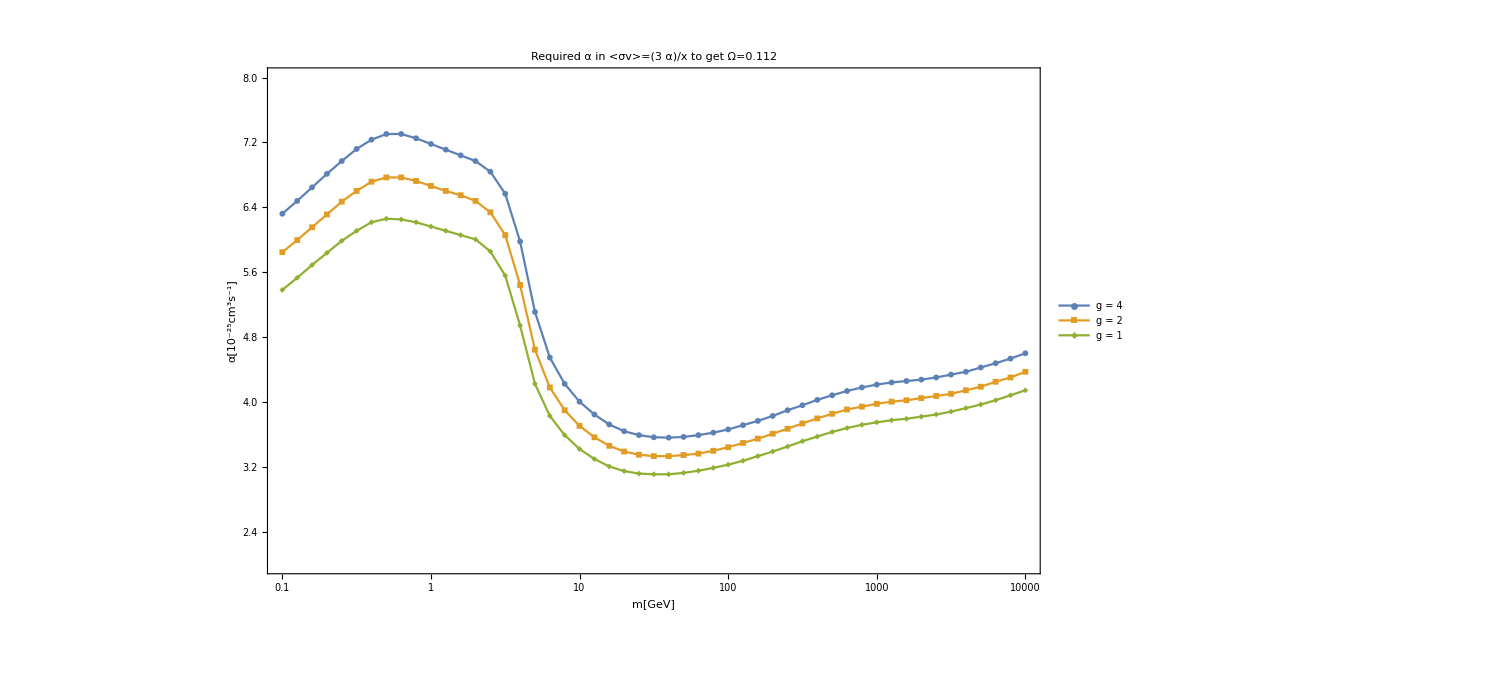

```mathematica
file7= Import["C:\\Users\\AlexandrePoulin\\Documents\\relic\\freezeout_v2.2\\outputFiles\\outputOmegaPDatag4.txt","Data"];
file8= Import["C:\\Users\\AlexandrePoulin\\Documents\\relic\\freezeout_v2.2\\outputFiles\\outputOmegaPDatag2.txt","Data"];
file9= Import["C:\\Users\\AlexandrePoulin\\Documents\\relic\\freezeout_v2.2\\outputFiles\\outputOmegaPDatag1.txt","Data"];
plotDataOmegag4= Table[{file7[[a]][[1]],file7[[a]][[2]]*10^(25)/3},{a,Length[file7]}];
plotDataOmegag2= Table[{file8[[a]][[1]],file8[[a]][[2]]*10^(25)/3},{a,Length[file8]}];
plotDataOmegag1= Table[{file9[[a]][[1]],file9[[a]][[2]]*10^(25)/3},{a,Length[file9]}];
p=ListLogLinearPlot[{plotDataOmegag4,plotDataOmegag2,plotDataOmegag1},PlotRange->{{10^-1,10^4},{2,8}}(*PlotRange->{{4,4.5},{0,6}}*),BaseStyle->{FontSize->20},PlotMarkers->{Automatic,6},ImageSize->{1100,750},AxesStyle->Thick,TicksStyle->Thick(*,PlotStyle->{RGBColor[0.7,0.7,0.7],RGBColor[0.7,0.7,0.7],Black,Red},Filling->{1->{2}}*),FillingStyle->{RGBColor[0.7,0.7,0.7]},Joined->True,PlotLegends->{"g = 4","g = 2" , "g = 1"}];
Show[p,FrameStyle->Thick,FrameTicksStyle->Thick,BaseStyle->{FontSize->40},Frame-> True,FrameLabel->{"m[GeV]","α[10^-25cm^3s^-1]"}, PlotLabel->"Required α in <σv>=(3  α)/x to get Ω=0.112"]
```

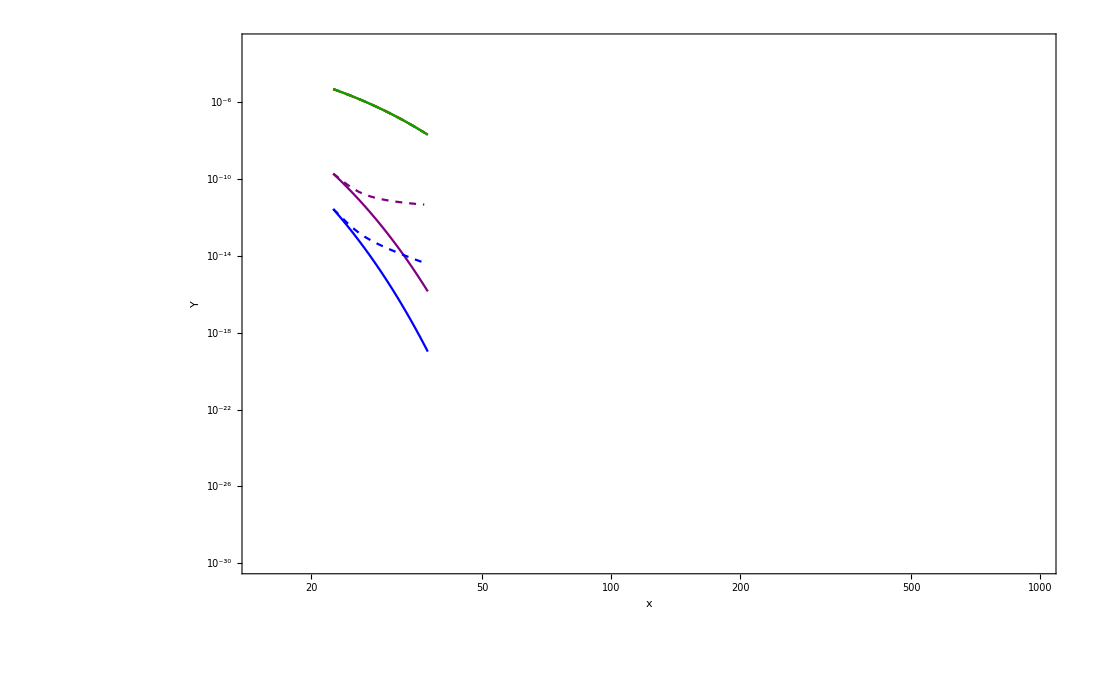

```mathematica
file= Import["C:\\Users\\AlexandrePoulin\\Documents\\relic\\freezeout_v2.5\\outputFiles\\outputOmega17.txt","Data"];

numDM = 4;
plotStyle = {Red,Darker[Green],Purple, Blue,{Red,Dashed},{Darker[Green],Dashed},{Dashed,Purple},{Dashed,Blue}};
(*plotStyle = {Red,White,White,White,White, White,White,{Red},{White,Dashed},{White,Dashed},{White,Dashed},{White,Purple},{White,Magenta},{White,Cyan}};*)

massScale=600.;
(*should get 0.110 and 0.0128 for omegas *)

plotDataeq = Table[Table[{massScale/file[[a]][[1]],file[[a]][[2*b]]},{a,Length[file]}],{b,1,numDM}];
plotData= Table[Table[{massScale/file[[a]][[1]],file[[a]][[2*b+1]]},{a,Length[file]}],{b,1,numDM}];

plot1=ListLogLogPlot[Join[plotDataeq,plotData],PlotRange->{{15,1000},{10^(-30),10^-3}},Joined->True,PlotStyle->plotStyle(*,Plot
Legends->{"Y_eq","Y"}*),BaseStyle->{FontSize->20},ImageSize->{1100,750},AxesStyle->Thick];
Show[plot1,FrameStyle->Thick,FrameTicksStyle->Thick,BaseStyle->{FontSize->40},Frame-> True,FrameLabel->{"x","Y"}]
```

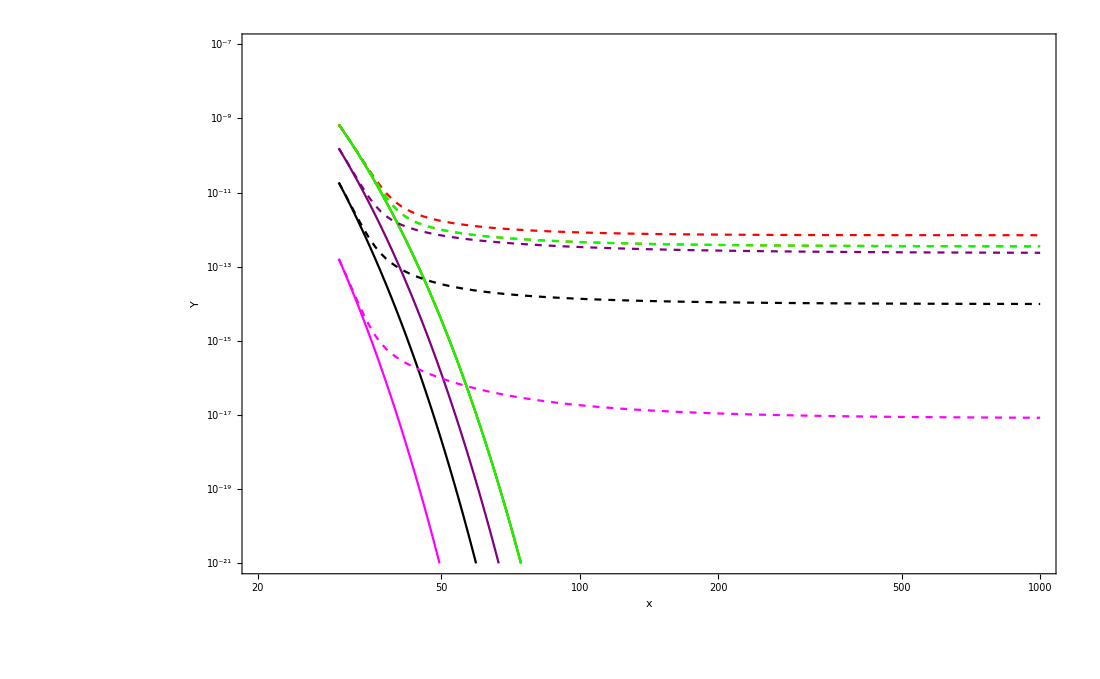

```mathematica
(*file= Import["C:\\Users\\AlexandrePoulin\\Documents\\relic\\freezeout_v2.5\\outputFiles\\outputOmega2.txt","Data"];
numDM = 3;
plotStyle = {Red,Green,Blue,{Red,Dashed},{Green,Dashed},{Blue,Dashed}};
massScale=600;*)


(*file= Import["C:\\Users\\AlexandrePoulin\\Documents\\relic\\freezeout_v2.5\\outputFiles\\outputOmega1.txt","Data"];
numDM = 3;
plotStyle = {Red,Green,Blue,{Red,Dashed},{Green,Dashed},{Blue,Dashed}};
massScale=300;*)

file= Import["C:\\Users\\AlexandrePoulin\\Documents\\relic\\freezeout_v2.5\\outputFiles\\outputOmega4.txt","Data"];
numDM = 6;
massScale=390;
plotStyle = {Red,Orange,Green,Black,Purple, Magenta,{Red,Dashed},{Orange,Dashed},{Green,Dashed},{Black,Dashed},{Dashed,Purple},{Dashed,Magenta}};


(*file= Import["C:\\Users\\AlexandrePoulin\\Documents\\relic\\freezeout_v2.5\\outputFiles\\outputOmega3.txt","Data"];
numDM = 8;
massScale=312.40998704;
plotStyle = {Red,Orange,Green,Black,Purple, Magenta,Blue, Brown,{Red,Dashed},{Orange,Dashed},{Green,Dashed},{Black,Dashed},{Dashed,Purple},{Dashed,Magenta},{Dashed,Blue},{Dashed,Brown}};*)



(*should get 0.110 and 0.0128 for omegas *)

plotDataeq = Table[Table[{massScale/file[[a]][[1]],file[[a]][[2*b]]},{a,Length[file]}],{b,1,numDM}];
plotData= Table[Table[{massScale/file[[a]][[1]],file[[a]][[2*b+1]]},{a,Length[file]}],{b,1,numDM}];

plot1=ListLogLogPlot[Join[plotDataeq,plotData],PlotRange->{{20,1000},{10^(-21),10^-7}},Joined->True,PlotStyle->plotStyle(*,Plot
Legends->{"Y_eq","Y"}*),BaseStyle->{FontSize->20},ImageSize->{1100,750},AxesStyle->Thick];
Show[plot1,FrameStyle->Thick,FrameTicksStyle->Thick,BaseStyle->{FontSize->40},Frame-> True,FrameLabel->{"x","Y"}]
```

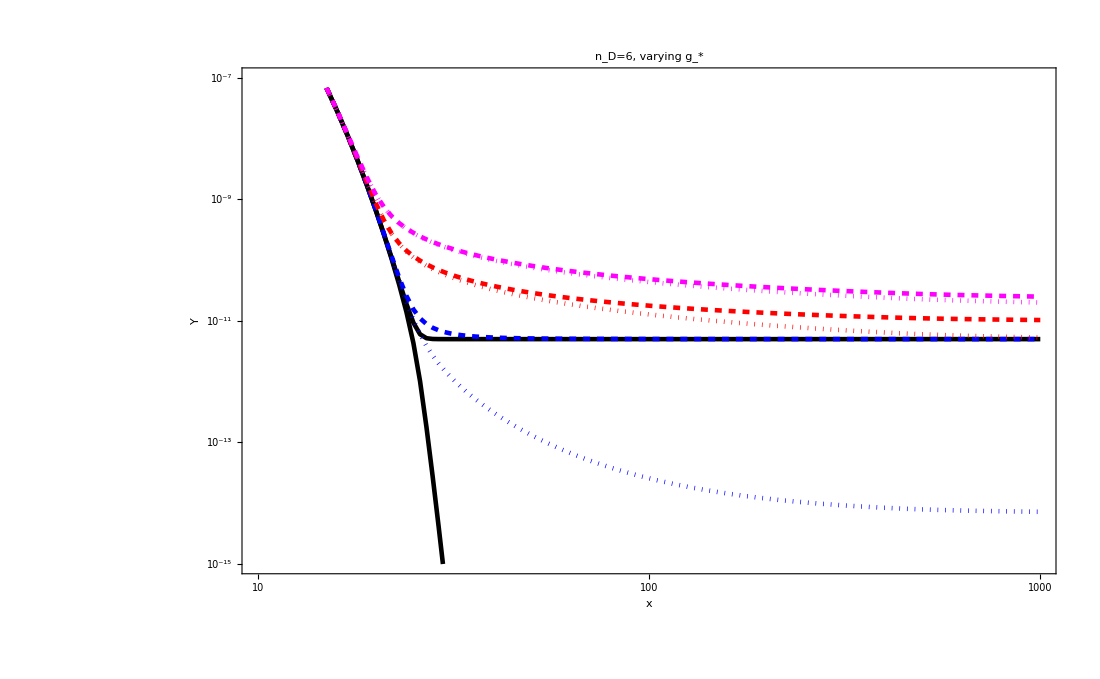

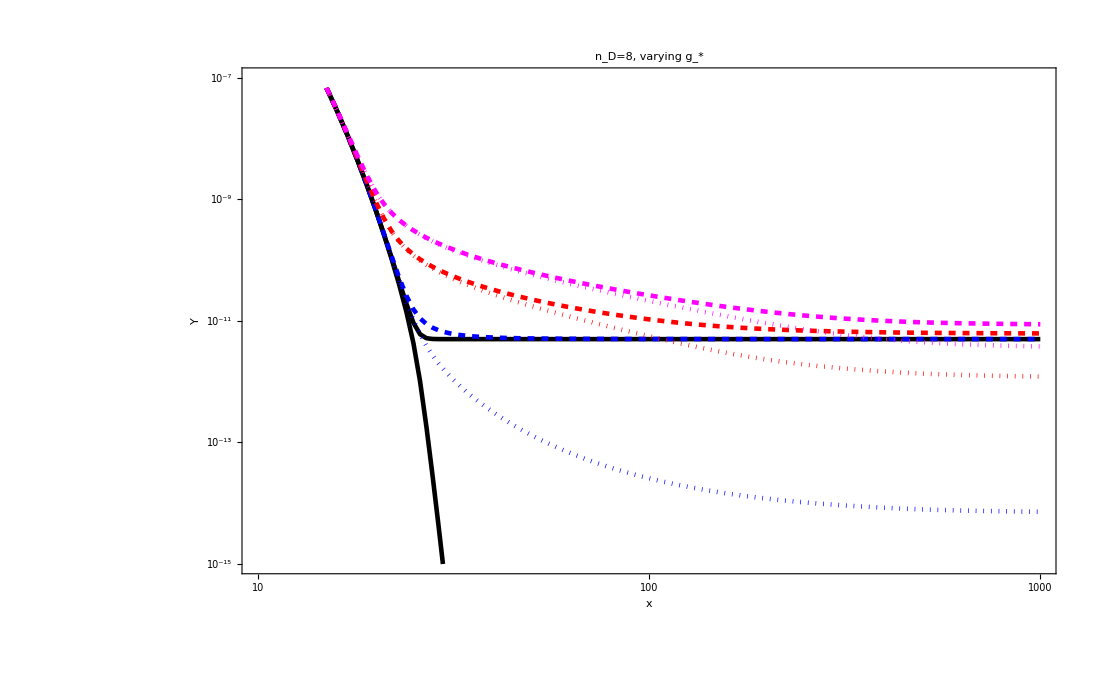

```mathematica
file1= Import["C:\\Users\\AlexandrePoulin\\Documents\\relic\\freezeout_v2.5\\Results\\assym\\outputOmega_0_new.txt","Data"];
file2= Import["C:\\Users\\AlexandrePoulin\\Documents\\relic\\freezeout_v2.5\\Results\\assym\\outputOmegaA_103_new.txt","Data"];
file3= Import["C:\\Users\\AlexandrePoulin\\Documents\\relic\\freezeout_v2.5\\Results\\assym\\outputOmegaA_104_new.txt","Data"];
file4= Import["C:\\Users\\AlexandrePoulin\\Documents\\relic\\freezeout_v2.5\\Results\\assym\\outputOmegaB_103_new.txt","Data"];
file5= Import["C:\\Users\\AlexandrePoulin\\Documents\\relic\\freezeout_v2.5\\Results\\assym\\outputOmegaB_104_new.txt","Data"];


numDM = 2;

thickness=0.003;
plotStyle = {{Black,Thickness[thickness]},{Black,Thickness[thickness]},{Blue,Dashed,Thickness[thickness]},{Blue,Dotted,Thickness[thickness]},{Red,Dashed,Thickness[thickness]},{Red,Dotted,Thickness[thickness]},{Magenta,Dashed,Thickness[thickness]},{Magenta,Dotted,Thickness[thickness]}};
(*plotStyle = {Red,White,White,White,White, White,White,{Red},{White,Dashed},{White,Dashed},{White,Dashed},{White,Purple},{White,Magenta},{White,Cyan}};*)

massScale=100;
(*should get 0.110 and 0.0128 for omegas *)

plotData1eq = Table[Table[{massScale/file1[[a]][[1]],file1[[a]][[2*b]]},{a,Length[file1]}],{b,1,numDM}];
plotData1= Table[Table[{massScale/file1[[a]][[1]],file1[[a]][[2*b+1]]},{a,Length[file1]}],{b,1,numDM}];
plotData2eq = Table[Table[{massScale/file2[2[a]][[1]],file2[[a]][[2*b]]},{a,Length[file2]}],{b,1,numDM}];
plotData2= Table[Table[{massScale/file2[[a]][[1]],file2[[a]][[2*b+1]]},{a,Length[file2]}],{b,1,numDM}];
plotData3eq = Table[Table[{massScale/file3[[a]][[1]],file3[[a]][[2*b]]},{a,Length[file3]}],{b,1,numDM}];
plotData3= Table[Table[{massScale/file3[[a]][[1]],file3[[a]][[2*b+1]]},{a,Length[file3]}],{b,1,numDM}];
plotData4eq = Table[Table[{massScale/file4[[a]][[1]],file4[[a]][[2*b]]},{a,Length[file4]}],{b,1,numDM}];
plotData4= Table[Table[{massScale/file4[[a]][[1]],file4[[a]][[2*b+1]]},{a,Length[file4]}],{b,1,numDM}];
plotData5eq = Table[Table[{massScale/file5[[a]][[1]],file5[[a]][[2*b]]},{a,Length[file5]}],{b,1,numDM}];
plotData5= Table[Table[{massScale/file5[[a]][[1]],file5[[a]][[2*b+1]]},{a,Length[file5]}],{b,1,numDM}];

plot1=ListLogLogPlot[Join[plotData1eq,plotData1,plotData2,plotData3],PlotRange->{{10,1000},{10^(-15),10^-7}},Joined->True,PlotStyle->plotStyle(*,Plot
Legends->{"Y_eq","Y"}*),BaseStyle->{FontSize->20},ImageSize->{1100,750},AxesStyle->Thick];
Show[plot1,FrameStyle->Thick,FrameTicksStyle->Thick,BaseStyle->{FontSize->40},Frame-> True,FrameLabel->{"x","Y"},PlotLabel->"n_D=6, varying g_*"]

plot2=ListLogLogPlot[Join[plotData1eq,plotData1,plotData4,plotData5],PlotRange->{{10,1000},{10^(-15),10^-7}},Joined->True,PlotStyle->plotStyle(*,Plot
Legends->{"Y_eq","Y"}*),BaseStyle->{FontSize->20},ImageSize->{1100,750},AxesStyle->Thick];
Show[plot2,FrameStyle->Thick,FrameTicksStyle->Thick,BaseStyle->{FontSize->40},Frame-> True,FrameLabel->{"x","Y"},PlotLabel->"n_D=8, varying g_*"]
```

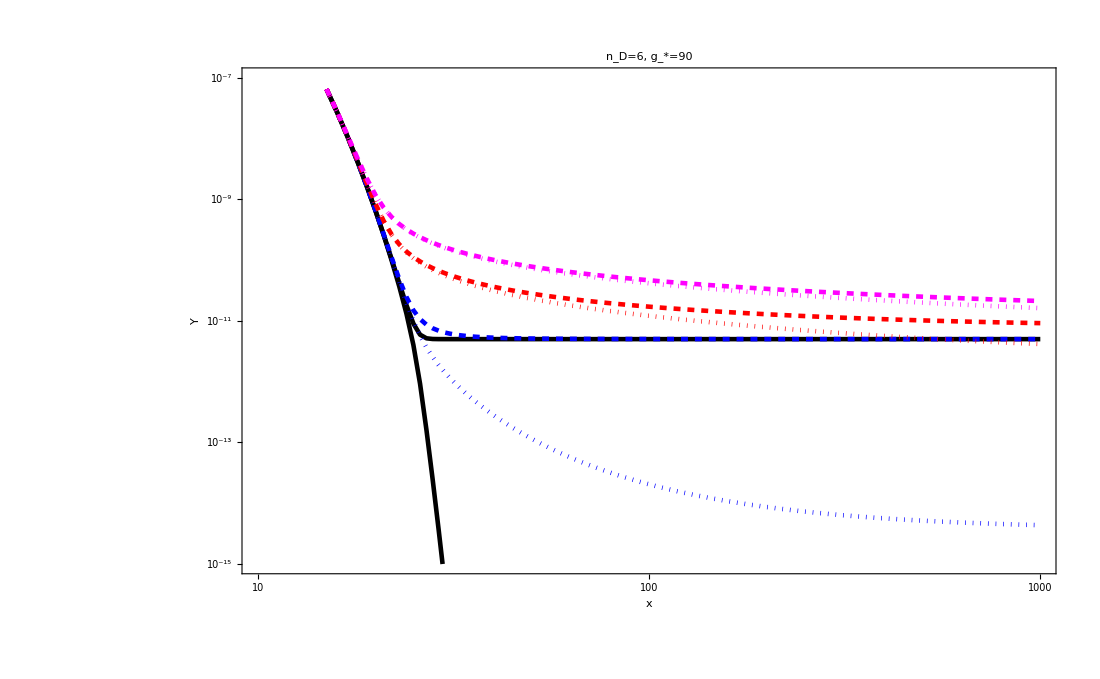

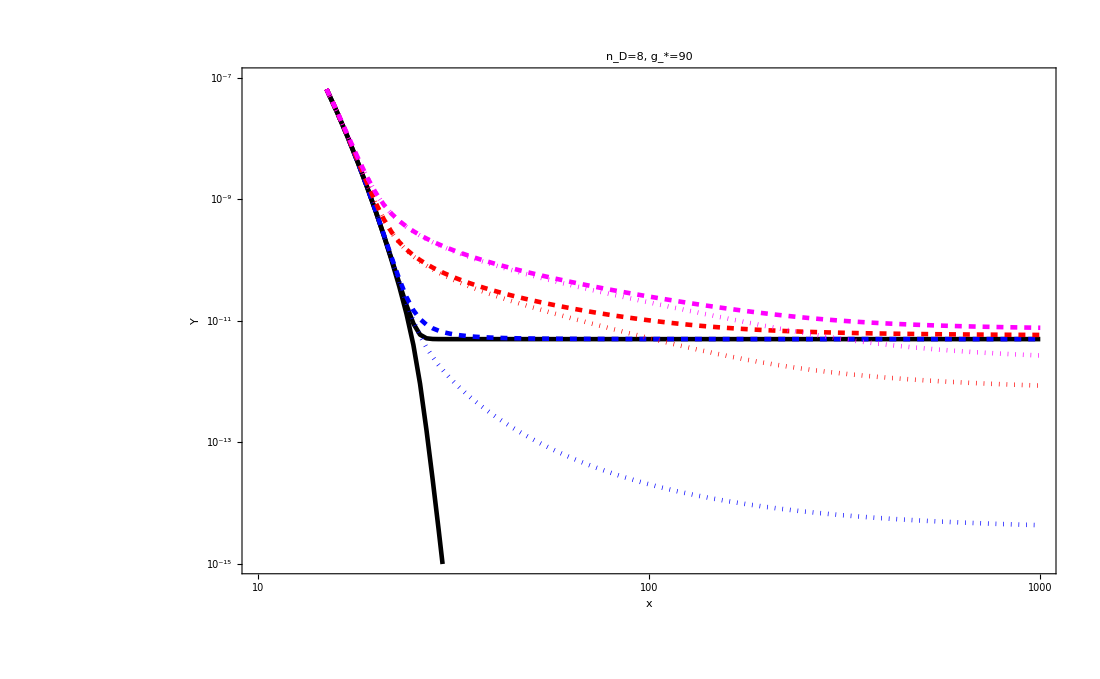

```mathematica
file1= Import["C:\\Users\\AlexandrePoulin\\Documents\\relic\\freezeout_v2.5\\Results\\assym\\outputOmega_0.txt","Data"];
file2= Import["C:\\Users\\AlexandrePoulin\\Documents\\relic\\freezeout_v2.5\\Results\\assym\\outputOmegaA_103.txt","Data"];
file3= Import["C:\\Users\\AlexandrePoulin\\Documents\\relic\\freezeout_v2.5\\Results\\assym\\outputOmegaA_104.txt","Data"];
file4= Import["C:\\Users\\AlexandrePoulin\\Documents\\relic\\freezeout_v2.5\\Results\\assym\\outputOmegaB_103.txt","Data"];
file5= Import["C:\\Users\\AlexandrePoulin\\Documents\\relic\\freezeout_v2.5\\Results\\assym\\outputOmegaB_104.txt","Data"];


numDM = 2;

thickness=0.003;
plotStyle = {{Black,Thickness[thickness]},{Black,Thickness[thickness]},{Blue,Dashed,Thickness[thickness]},{Blue,Dotted,Thickness[thickness]},{Red,Dashed,Thickness[thickness]},{Red,Dotted,Thickness[thickness]},{Magenta,Dashed,Thickness[thickness]},{Magenta,Dotted,Thickness[thickness]}};
(*plotStyle = {Red,White,White,White,White, White,White,{Red},{White,Dashed},{White,Dashed},{White,Dashed},{White,Purple},{White,Magenta},{White,Cyan}};*)

massScale=100;
(*should get 0.110 and 0.0128 for omegas *)

plotData1eq = Table[Table[{massScale/file1[[a]][[1]],file1[[a]][[2*b]]},{a,Length[file1]}],{b,1,numDM}];
plotData1= Table[Table[{massScale/file1[[a]][[1]],file1[[a]][[2*b+1]]},{a,Length[file1]}],{b,1,numDM}];
plotData2eq = Table[Table[{massScale/file2[2[a]][[1]],file2[[a]][[2*b]]},{a,Length[file2]}],{b,1,numDM}];
plotData2= Table[Table[{massScale/file2[[a]][[1]],file2[[a]][[2*b+1]]},{a,Length[file2]}],{b,1,numDM}];
plotData3eq = Table[Table[{massScale/file3[[a]][[1]],file3[[a]][[2*b]]},{a,Length[file3]}],{b,1,numDM}];
plotData3= Table[Table[{massScale/file3[[a]][[1]],file3[[a]][[2*b+1]]},{a,Length[file3]}],{b,1,numDM}];
plotData4eq = Table[Table[{massScale/file4[[a]][[1]],file4[[a]][[2*b]]},{a,Length[file4]}],{b,1,numDM}];
plotData4= Table[Table[{massScale/file4[[a]][[1]],file4[[a]][[2*b+1]]},{a,Length[file4]}],{b,1,numDM}];
plotData5eq = Table[Table[{massScale/file5[[a]][[1]],file5[[a]][[2*b]]},{a,Length[file5]}],{b,1,numDM}];
plotData5= Table[Table[{massScale/file5[[a]][[1]],file5[[a]][[2*b+1]]},{a,Length[file5]}],{b,1,numDM}];

plot1=ListLogLogPlot[Join[plotData1eq,plotData1,plotData2,plotData3],PlotRange->{{10,1000},{10^(-15),10^-7}},Joined->True,PlotStyle->plotStyle(*,Plot
Legends->{"Y_eq","Y"}*),BaseStyle->{FontSize->20},ImageSize->{1100,750},AxesStyle->Thick];
Show[plot1,FrameStyle->Thick,FrameTicksStyle->Thick,BaseStyle->{FontSize->40},Frame-> True,FrameLabel->{"x","Y"},PlotLabel->"n_D=6, g_*=90"]

plot2=ListLogLogPlot[Join[plotData1eq,plotData1,plotData4,plotData5],PlotRange->{{10,1000},{10^(-15),10^-7}},Joined->True,PlotStyle->plotStyle(*,Plot
Legends->{"Y_eq","Y"}*),BaseStyle->{FontSize->20},ImageSize->{1100,750},AxesStyle->Thick];
Show[plot2,FrameStyle->Thick,FrameTicksStyle->Thick,BaseStyle->{FontSize->40},Frame-> True,FrameLabel->{"x","Y"},PlotLabel->"n_D=8, g_*=90"]
```

```mathematica
0.0763+0.03014+0.01711
```

0.12355

```mathematica
Head[10^-12]
Head[10.^-12]
```

Rational

Real

```mathematica
10.^-12
```

```mathematica
Rationalize[10.^-12, 10^-15]
```

Rational

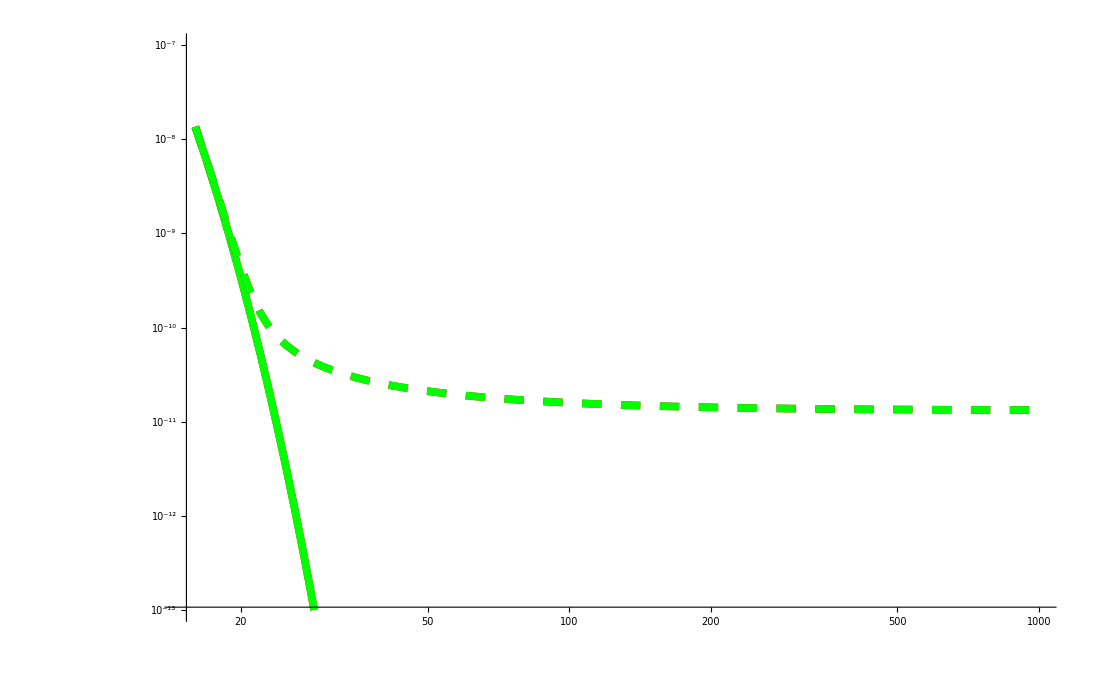

```mathematica
getTicks[pl_]:=Block[{},
tx=Map[MapAt[3#&,#,3]&,Ticks/.AbsoluteOptions[pl,Ticks],{2}];
tx=Map[MapAt[{GrayLevel[0.],AbsoluteThickness[3]}&,#,4]&,tx,{2}];
tx=Map[MapAt[Rationalize[#,10^-15]&,#,2]&,tx,{2}];
{tx[[1]],tx[[2]],None,None}
]

file= Import["C:\\Users\\AlexandrePoulin\\Documents\\relic\\freezeout_v2.5\\outputFiles\\outputDataTest.txt","Data"];

numDM = 2;

thick=Thickness[0.005];
dashed=Dashing[Large];
dotdash=Dashing[{0,Large,Large,Large}];
plotStyle = {{Red,thick},{Green,thick},{Red,thick,dashed},{Green,thick,dashed}};
plotStyle2 = {{Red,thick,dotdash},{Blue,thick,dotdash}};

massScale=100;
(*should get 0.110 and 0.0128 for omegas *)

plotDataeq = Table[Table[{massScale/file[[a]][[1]],file[[a]][[2*b]]},{a,Length[file]}],{b,1,numDM}];
plotData= Table[Table[{massScale/file[[a]][[1]],file[[a]][[2*b+1]]},{a,Length[file]}],{b,1,numDM}];





plot1=ListLogLogPlot[Join[plotDataeq,plotData],PlotRange->{{15,1000},{10^(-13),10^-7}},Joined->True,PlotStyle->plotStyle(*,PlotLegends->{"Y_eq","Y"}*),BaseStyle->{FontSize->20},ImageSize->{1100,750},AxesStyle->Thick]
```

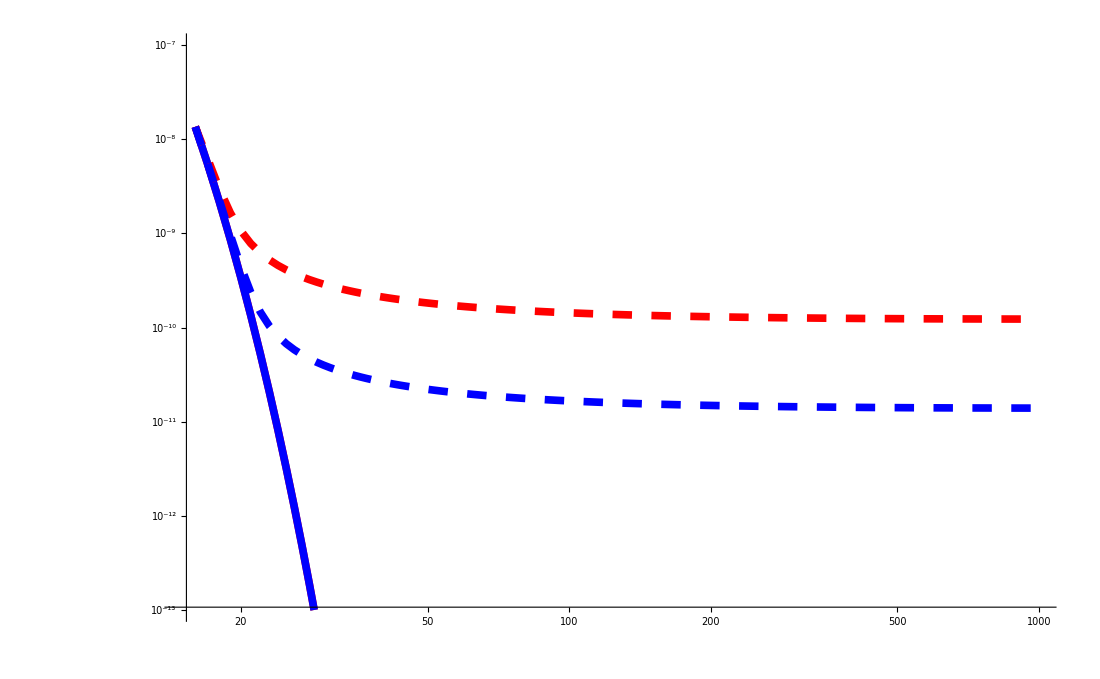

```mathematica
getTicks[pl_]:=Block[{},
tx=Map[MapAt[3#&,#,3]&,Ticks/.AbsoluteOptions[pl,Ticks],{2}];
tx=Map[MapAt[{GrayLevel[0.],AbsoluteThickness[3]}&,#,4]&,tx,{2}];
tx=Map[MapAt[Rationalize[#,10^-15]&,#,2]&,tx,{2}];
{tx[[1]],tx[[2]],None,None}
]

file= Import["C:\\Users\\AlexandrePoulin\\Documents\\relic\\freezeout_v2.5\\outputFiles\\outputDataTest2.txt","Data"];

numDM = 2;

thick=Thickness[0.005];
dashed=Dashing[Large];
dotdash=Dashing[{0,Large,Large,Large}];
plotStyle = {{Red,thick},{Blue,thick},{Red,thick,dashed},{Blue,thick,dashed}};
plotStyle2 = {{Red,thick,dotdash},{Blue,thick,dotdash}};

massScale=100;
(*should get 0.110 and 0.0128 for omegas *)

plotDataeq = Table[Table[{massScale/file[[a]][[1]],file[[a]][[2*b]]},{a,Length[file]}],{b,1,numDM}];
plotData= Table[Table[{massScale/file[[a]][[1]],file[[a]][[2*b+1]]},{a,Length[file]}],{b,1,numDM}];





plot2=ListLogLogPlot[Join[plotDataeq,plotData],PlotRange->{{15,1000},{10^(-13),10^-7}},Joined->True,PlotStyle->plotStyle(*,PlotLegends->{"Y_eq","Y"}*),BaseStyle->{FontSize->20},ImageSize->{1100,750},AxesStyle->Thick]
```

Axes::axes: {2.72905, {Thickness[Large]}} is not a valid axis specification.

Axes::axes: {-29.8645, {Thickness[Large]}} is not a valid axis specification.

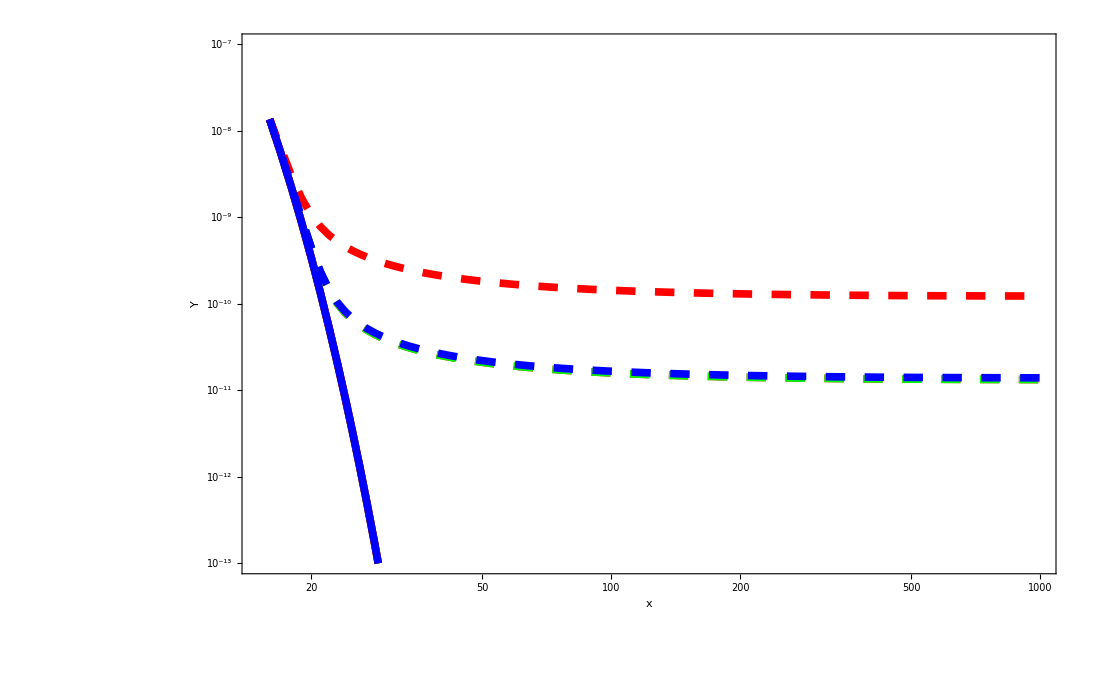

```mathematica
Show[{plot1,plot2},FrameStyle->Thickness[0.005],FrameTicks->getTicks[plot1],BaseStyle->{FontSize->50},Frame-> True,FrameLabel->{"x"," Y"},LabelStyle->Black]
```

```mathematica
(1.23169*10^-10)/(2*1.33241*10^(-11))
(0.139553*10^-10)/(2*1.33241*10^(-11))
```

4.62204

0.523686

```mathematica
gstar=0.1;
mpl=1.22*10^19;
m=100;
sig1=0.02/(0.3894*10^9);

xf1=Quiet[x/.NSolve[x==Log[0.038*m*mpl*sig1/Sqrt[gstar*x]],{x}][[1]][[1]]];

sig2=0.2/(0.3894*10^9);

xf2=Quiet[x/.NSolve[x==Log[0.038*m*mpl*sig2/Sqrt[gstar*x]],{x}][[1]][[1]]];

geff=2;
sigEff=(0.02+0.2+0.2)/geff^2/(0.3894*10^9);

xfEff=Quiet[x/.NSolve[x==Log[0.038*geff*m*mpl*sigEff/Sqrt[gstar*x]],{x}][[1]][[1]]];

ratioOldOverNew=(xf1/sig1)/(xfEff/sigEff)
```

4.73651

```mathematica
(2*1.33241*10^(-11))*6.707677210319365
```

1.78748×10^-10

```mathematica
(xf1/sig1)/(xf2/sig2)
```

8.94101

```mathematica
1.23169/0.139553
```

8.82597

```mathematica
(xf2/sig2)/(xfEff/sigEff)
```

0.523823

```mathematica
xf1
xf2
xfEff
```

17.8473

20.0907

20.1383

```mathematica
2*1.33241*10^(-11)
```

2.66482×10^-11

Axes::axes: {2.72905, {Thickness[Large]}} is not a valid axis specification.

Axes::axes: {-29.8645, {Thickness[Large]}} is not a valid axis specification.

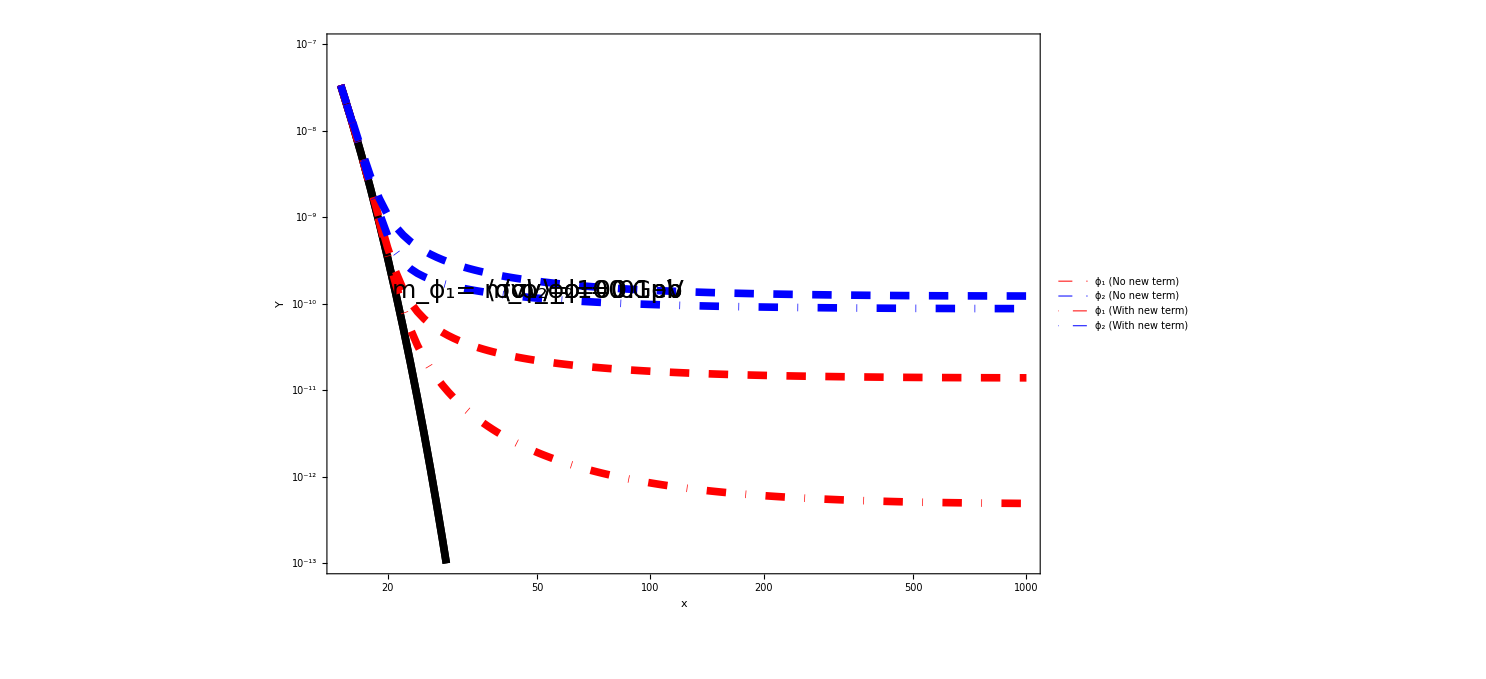

Axes::axes: {2.72905, {Thickness[Large]}} is not a valid axis specification.

Axes::axes: {-29.8645, {Thickness[Large]}} is not a valid axis specification.

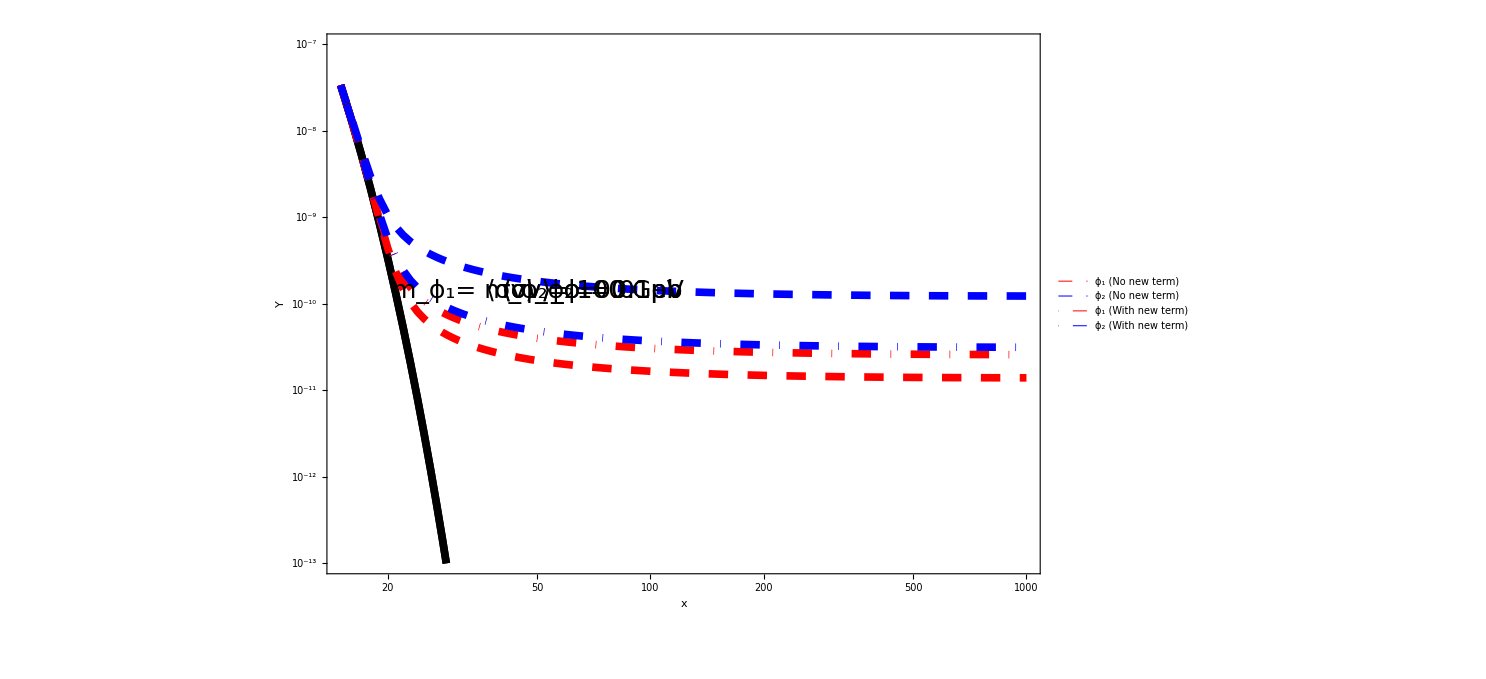

```mathematica
getTicks[pl_]:=Block[{},
tx=Map[MapAt[3#&,#,3]&,Ticks/.AbsoluteOptions[pl,Ticks],{2}];
tx=Map[MapAt[{GrayLevel[0.],AbsoluteThickness[3]}&,#,4]&,tx,{2}];
tx=Map[MapAt[Rationalize[#,10^-15]&,#,2]&,tx,{2}];
{tx[[1]],tx[[2]],None,None}
]

simpleLegend[legendItems__,pos_]:=Module[{legendLine,offset,legend},offset=Module[{s,o,insetpts=10},s=pos/.{Left->0,Right->1,Bottom->0,Top->1};
o=insetpts pos/.{Left->1,Right->-1,Bottom->1,Top->-1};
Offset[o,Scaled[s]]];
legendLine[{lbl_,lineStyle_}]:={Graphics[{lineStyle,Line[{{0,0.5},{1,0.5}}]},ImageSize->{20,10},AspectRatio->0.5],Style[lbl,FontFamily->"Tahoma",FontSize->11,TextAlignment->Left,LineBreakWithin->False]};
legend=GraphicsGrid[legendLine/@legendItems,Alignment->Left];
Graphics@Inset[legend,offset,pos]];

file= Import["C:\\Users\\AlexandrePoulin\\Documents\\relic\\freezeout_v2.5\\outputFiles\\waveTest\\outputOmegaBase.txt","Data"];
file2= Import["C:\\Users\\AlexandrePoulin\\Documents\\relic\\freezeout_v2.5\\outputFiles\\waveTest\\outputOmegaCo.txt","Data"];
file3= Import["C:\\Users\\AlexandrePoulin\\Documents\\relic\\freezeout_v2.5\\outputFiles\\waveTest\\outputOmegaConv.txt","Data"];

numDM = 2;

thick=Thickness[0.005];
dashed=Dashing[Large];
dotdash=Dashing[{0,Large,Large,Large}];
plotStyle = {{Black,thick},{Black,thick},{Red,thick,dashed},{Blue,thick,dashed}};
plotStyle2 = {{Red,thick,dotdash},{Blue,thick,dotdash}};

massScale=100;
(*should get 0.110 and 0.0128 for omegas *)

plotDataeq = Table[Table[{massScale/file[[a]][[1]],file[[a]][[2*b]]},{a,Length[file]}],{b,1,numDM}];
plotData= Table[Table[{massScale/file[[a]][[1]],file[[a]][[2*b+1]]},{a,Length[file]}],{b,1,numDM}];

plotDataeq2 = Table[Table[{massScale/file2[[a]][[1]],file2[[a]][[2*b]]},{a,Length[file2]}],{b,1,numDM}];
plotData2= Table[Table[{massScale/file2[[a]][[1]],file2[[a]][[2*b+1]]},{a,Length[file2]}],{b,1,numDM}];

plotDataeq3 = Table[Table[{massScale/file3[[a]][[1]],file3[[a]][[2*b]]},{a,Length[file3]}],{b,1,numDM}];
plotData3= Table[Table[{massScale/file3[[a]][[1]],file3[[a]][[2*b+1]]},{a,Length[file3]}],{b,1,numDM}];


plot1=ListLogLogPlot[Join[plotDataeq,plotData],PlotRange->{{15,1000},{10^(-13),10^-7}},Joined->True,PlotStyle->plotStyle(*,PlotLegends->{"Y_eq","Y"}*),BaseStyle->{FontSize->20},ImageSize->{1100,750},AxesStyle->Thick,PlotLegends->Placed[LineLegend[{{Red,dashed,Thickness[0.01]},{Blue,dashed,Thickness[0.01]},{Red,dotdash,Thickness[0.01]},{Blue,dotdash,Thickness[0.01]},White},{"ϕ_1 (No new term)","ϕ_2 (No new term)","ϕ_1 (With new term)","ϕ_2 (With new term)"," "},LabelStyle->{25},LegendMarkerSize->{{100,20}}],{Right,Top}]];
plot2=ListLogLogPlot[plotData2,PlotRange->{{10,1000},{10^(-13),10^-7}},Joined->True,PlotStyle->plotStyle2(*,PlotLegends->{"Y_eq","Y"}*),BaseStyle->{FontSize->20},ImageSize->{1100,750},AxesStyle->Thick];
plot3=ListLogLogPlot[plotData3,PlotRange->{{10,1000},{10^(-13),10^-7}},Joined->True,PlotStyle->plotStyle2(*,PlotLegends->{"Y_eq","Y"}*),BaseStyle->{FontSize->20},ImageSize->{1100,750},AxesStyle->Thick];


Show[{plot1,plot2},FrameStyle->Thickness[0.005],FrameTicks->getTicks[plot1],BaseStyle->{FontSize->50},Frame-> True,FrameLabel->{"x"," Y"},LabelStyle->Black,Epilog->{Text[Style["m_ϕ_1= m_ϕ_2= 100 GeV",25,Black],Scaled[{0.5,0.5}],{1,-14}],
Text[Style["⟨σv⟩_ϕ_1=0.1pb",25,Black],Scaled[{0.5,0.5}],{1,-12}],
Text[Style["⟨σv⟩_ϕ_2=0.01pb",25,Black],Scaled[{0.5,0.5}],{1,-10}],
Text[Style["⟨σv⟩_ϕ_1=0.1pb",25,Black],Scaled[{0.5,0.5}],{1,-8}]}]
Show[{plot1,plot3},FrameStyle->Thickness[0.005],FrameTicks->getTicks[plot1],BaseStyle->{FontSize->50},Frame-> True,FrameLabel->{"x"," Y"},LabelStyle->Black,Epilog->{Text[Style["m_ϕ_1= m_ϕ_2= 100 GeV",25,Black],Scaled[{0.5,0.5}],{1,-14}],
Text[Style["⟨σv⟩_ϕ_1=0.1pb",25,Black],Scaled[{0.5,0.5}],{1,-12}],
Text[Style["⟨σv⟩_ϕ_2=0.01pb",25,Black],Scaled[{0.5,0.5}],{1,-10}],
Text[Style["⟨σv⟩_ϕ_1=0.1pb",25,Black],Scaled[{0.5,0.5}],{1,-8}]}]
```

Axes::axes: {2.72905, {Thickness[Large]}} is not a valid axis specification.

Axes::axes: {-34.4467, {Thickness[Large]}} is not a valid axis specification.

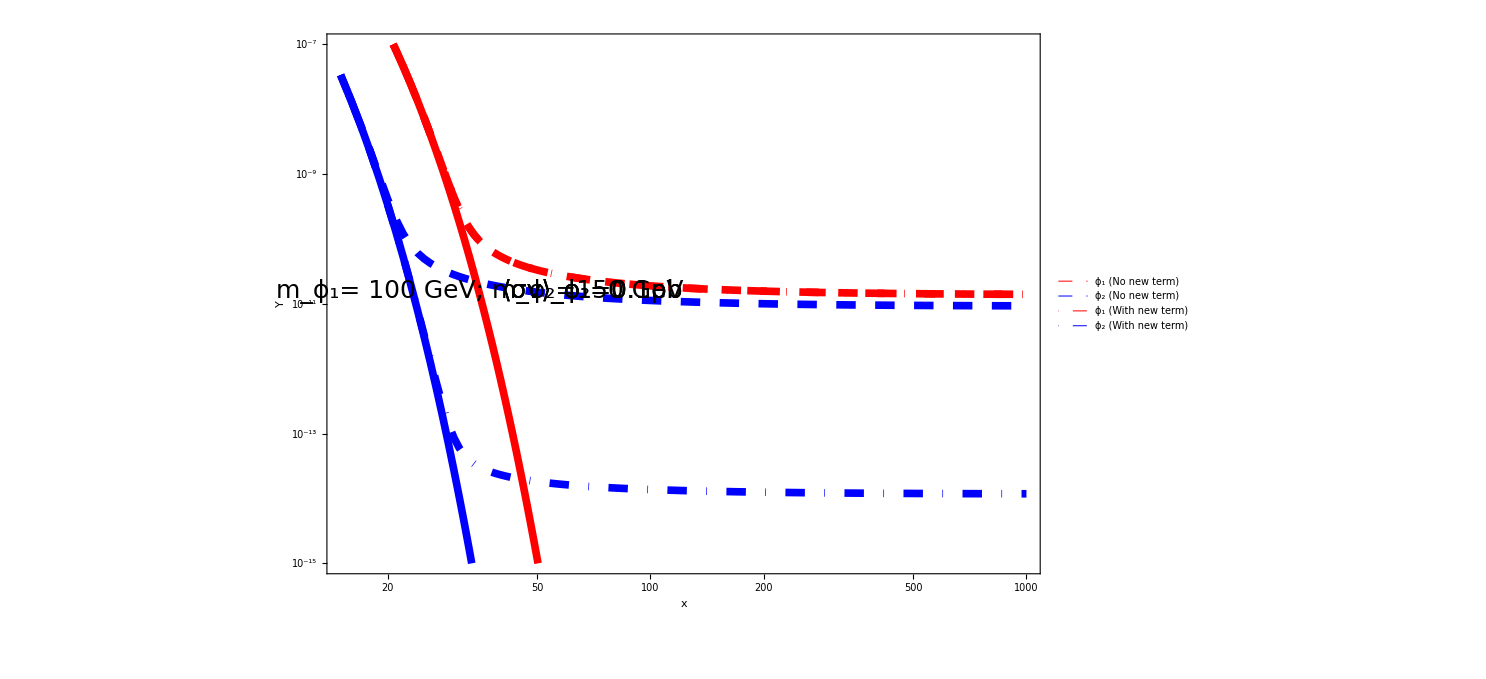

Axes::axes: {2.72905, {Thickness[Large]}} is not a valid axis specification.

Axes::axes: {-34.4467, {Thickness[Large]}} is not a valid axis specification.

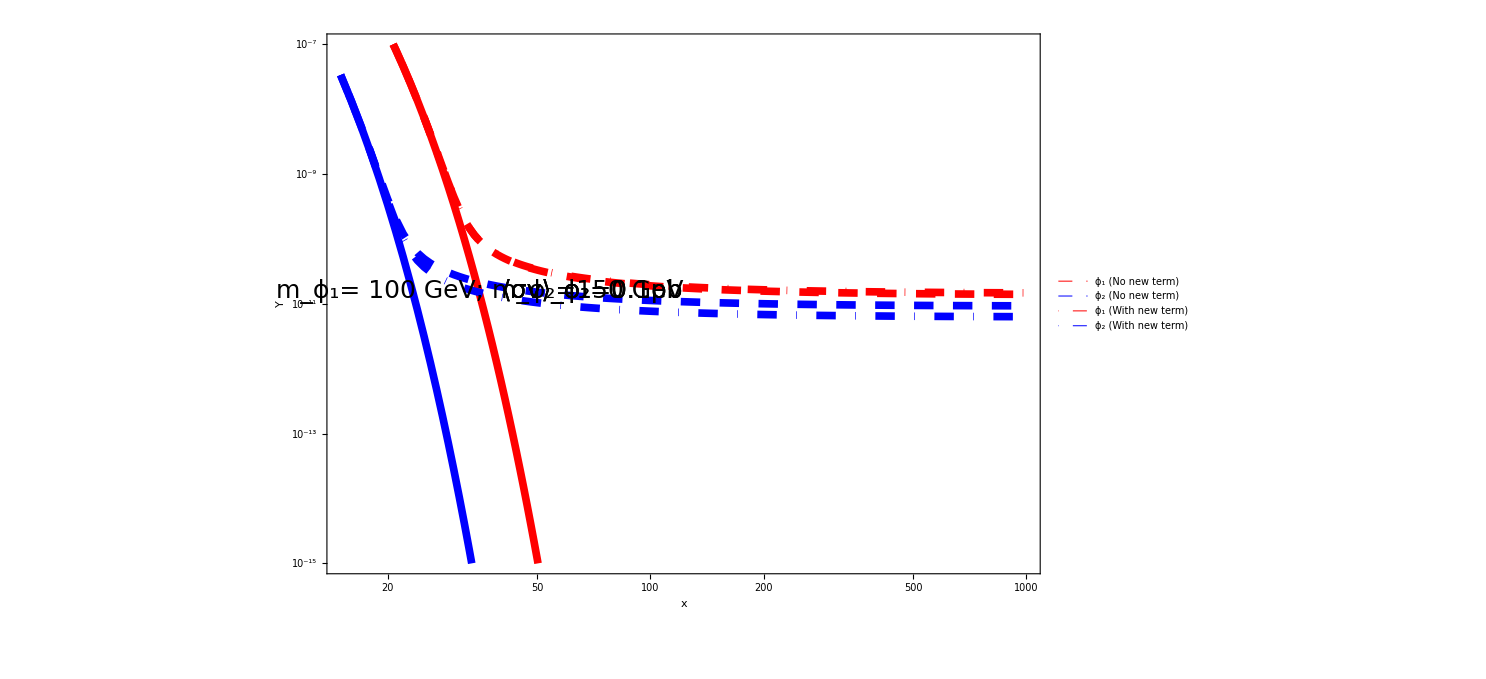

```mathematica
file= Import["C:\\Users\\AlexandrePoulin\\Documents\\relic\\freezeout_v2.5\\outputFiles\\waveTest\\outputOmegaDiffBase.txt","Data"];
file2= Import["C:\\Users\\AlexandrePoulin\\Documents\\relic\\freezeout_v2.5\\outputFiles\\waveTest\\outputOmegaDiffCo.txt","Data"];
file3= Import["C:\\Users\\AlexandrePoulin\\Documents\\relic\\freezeout_v2.5\\outputFiles\\waveTest\\outputOmegaDiffConv.txt","Data"];

numDM = 2;

thick=Thickness[0.005];
dashed=Dashing[Large];
dotdash=Dashing[{0,Large,Large,Large}];
plotStyle = {{Red,thick},{Blue,thick},{Red,thick,dashed},{Blue,thick,dashed}};
plotStyle2 = {{Blue,thick,dotdash},{Red,thick,dotdash}};
plotStyle3 = {{Red,thick,dotdash},{Blue,thick,dotdash}};

massScale=150;
(*should get 0.110 and 0.0128 for omegas *)

plotDataeq = Table[Table[{massScale/file[[a]][[1]],file[[a]][[2*b]]},{a,Length[file]}],{b,1,numDM}];
plotData= Table[Table[{massScale/file[[a]][[1]],file[[a]][[2*b+1]]},{a,Length[file]}],{b,1,numDM}];

plotDataeq2 = Table[Table[{massScale/file2[[a]][[1]],file2[[a]][[2*b]]},{a,Length[file2]}],{b,1,numDM}];
plotData2= Table[Table[{massScale/file2[[a]][[1]],file2[[a]][[2*b+1]]},{a,Length[file2]}],{b,1,numDM}];

plotDataeq3 = Table[Table[{massScale/file3[[a]][[1]],file3[[a]][[2*b]]},{a,Length[file3]}],{b,1,numDM}];
plotData3= Table[Table[{massScale/file3[[a]][[1]],file3[[a]][[2*b+1]]},{a,Length[file3]}],{b,1,numDM}];


plot1=ListLogLogPlot[Join[plotDataeq,plotData],PlotRange->{{15,1000},{10^(-15),10^-7}},Joined->True,PlotStyle->plotStyle(*,PlotLegends->{"Y_eq","Y"}*),BaseStyle->{FontSize->20},ImageSize->{1100,750},AxesStyle->Thick,PlotLegends->Placed[LineLegend[{{Red,dashed,Thickness[0.01]},{Blue,dashed,Thickness[0.01]},{Red,dotdash,Thickness[0.01]},{Blue,dotdash,Thickness[0.01]},White},{"ϕ_1 (No new term)","ϕ_2 (No new term)","ϕ_1 (With new term)","ϕ_2 (With new term)"," "},LabelStyle->{25},LegendMarkerSize->{{100,20}}],{Right,Top}]];
plot2=ListLogLogPlot[plotData2,PlotRange->{{10,1000},{10^(-15),10^-7}},Joined->True,PlotStyle->plotStyle3(*,PlotLegends->{"Y_eq","Y"}*),BaseStyle->{FontSize->20},ImageSize->{1100,750},AxesStyle->Thick];
plot3=ListLogLogPlot[plotData3,PlotRange->{{10,1000},{10^(-13),10^-7}},Joined->True,PlotStyle->plotStyle2(*,PlotLegends->{"Y_eq","Y"}*),BaseStyle->{FontSize->20},ImageSize->{1100,750},AxesStyle->Thick];
Show[{plot1,plot2},FrameStyle->Thickness[0.005],FrameTicks->getTicks[plot1],BaseStyle->{FontSize->50},Frame-> True,FrameLabel->{"x"," Y"},LabelStyle->Black,Epilog->{Text[Style["m_ϕ_1= 100 GeV; m_ϕ_2=150 GeV",25,Black],Scaled[{0.5,0.5}],{1,-14}],
Text[Style["⟨σv⟩_ϕ_1=0.1pb",25,Black],Scaled[{0.5,0.5}],{1,-12}],
Text[Style["⟨σv⟩_ϕ_2=0.1pb",25,Black],Scaled[{0.5,0.5}],{1,-10}],
Text[Style["⟨σv⟩_ϕ_1=0.1pb",25,Black],Scaled[{0.5,0.5}],{1,-8}]}]
Show[{plot1,plot3},FrameStyle->Thickness[0.005],FrameTicks->getTicks[plot1],BaseStyle->{FontSize->50},Frame-> True,FrameLabel->{"x"," Y"},LabelStyle->Black,Epilog->{Text[Style["m_ϕ_1= 100 GeV; m_ϕ_2=150 GeV",25,Black],Scaled[{0.5,0.5}],{1,-14}],
Text[Style["⟨σv⟩_ϕ_1=0.1pb",25,Black],Scaled[{0.5,0.5}],{1,-12}],
Text[Style["⟨σv⟩_ϕ_2=0.1pb",25,Black],Scaled[{0.5,0.5}],{1,-10}],
Text[Style["⟨σv⟩_ϕ_2=0.1pb",25,Black],Scaled[{0.5,0.5}],{1,-8}]}]
```

Axes::axes: {2.72905, {Thickness[Large]}} is not a valid axis specification.

Axes::axes: {-27.5504, {Thickness[Large]}} is not a valid axis specification.

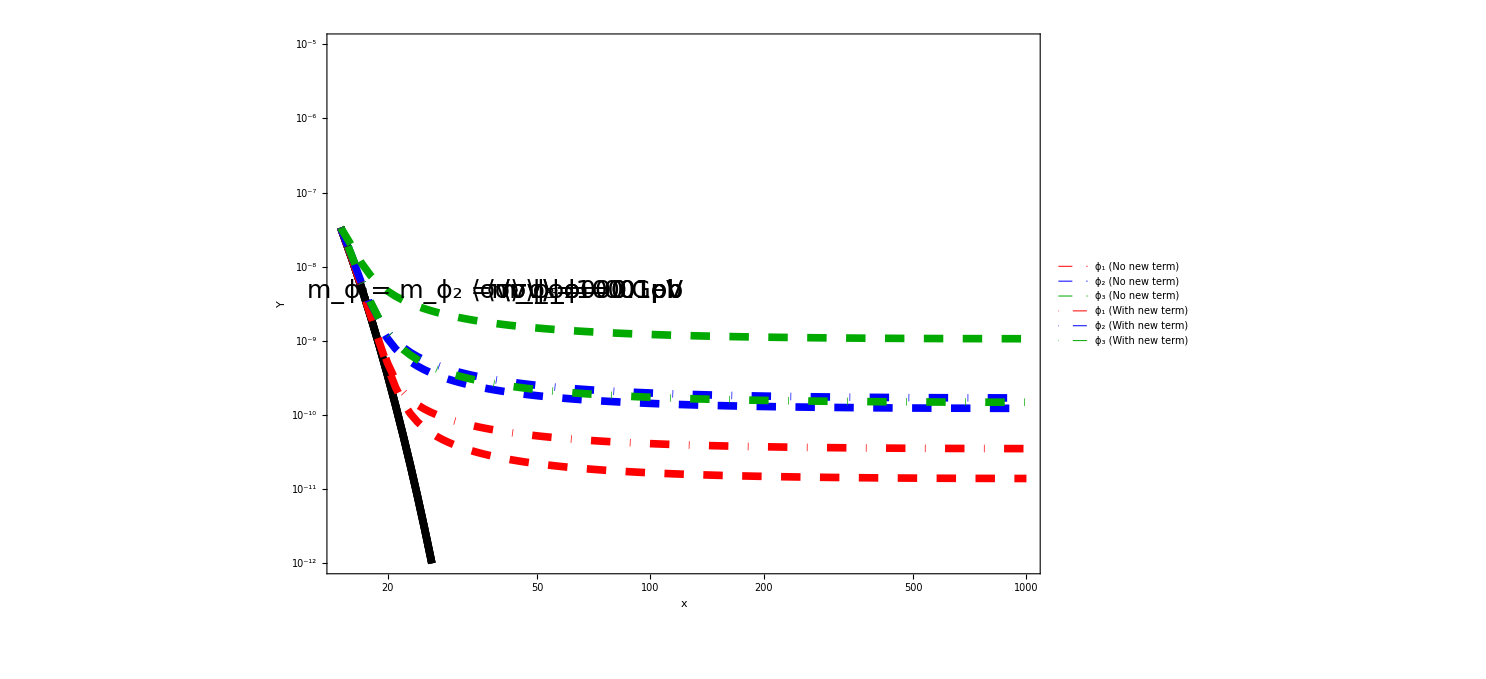

Axes::axes: {2.72905, {Thickness[Large]}} is not a valid axis specification.

Axes::axes: {-27.5504, {Thickness[Large]}} is not a valid axis specification.

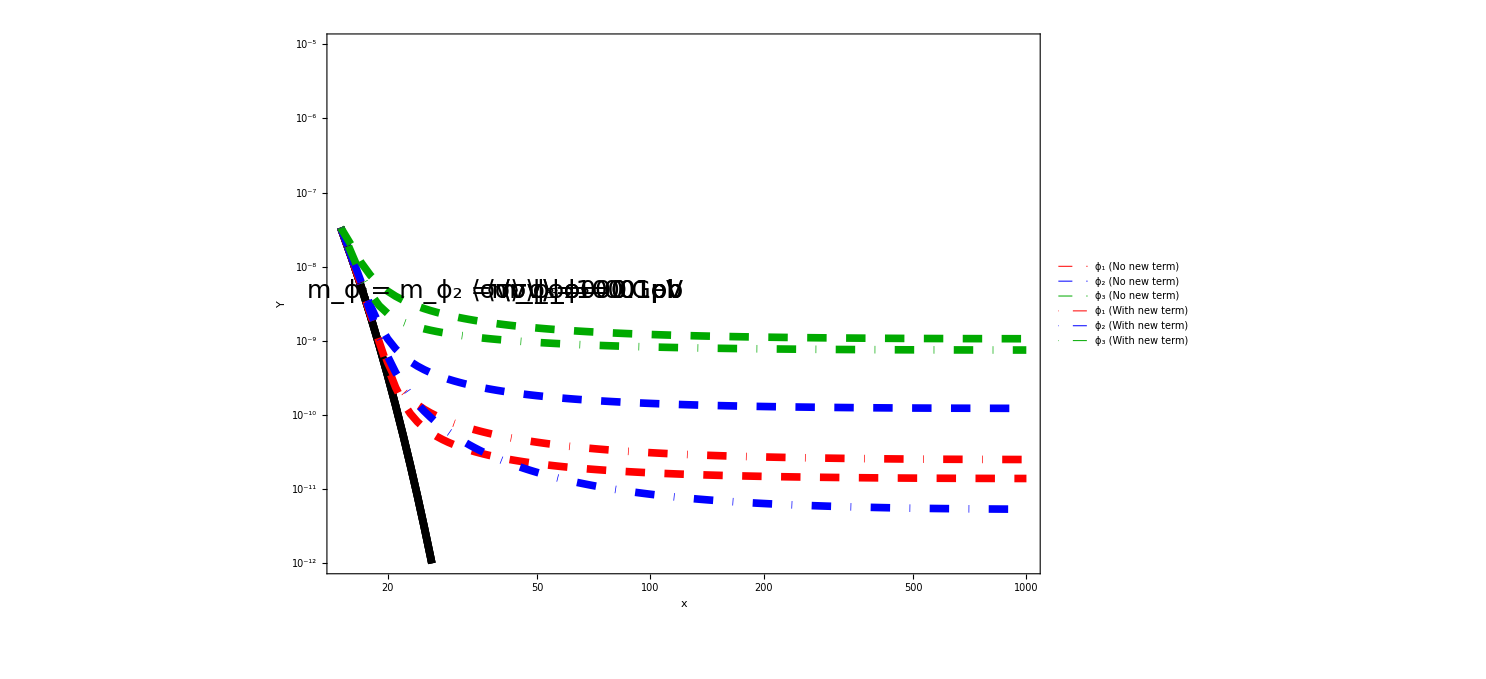

```mathematica
file= Import["C:\\Users\\AlexandrePoulin\\Documents\\relic\\freezeout_v2.5\\outputFiles\\waveTest\\outputOmegaBase3.txt","Data"];
file2= Import["C:\\Users\\AlexandrePoulin\\Documents\\relic\\freezeout_v2.5\\outputFiles\\waveTest\\outputOmega2to1.txt","Data"];
file3= Import["C:\\Users\\AlexandrePoulin\\Documents\\relic\\freezeout_v2.5\\outputFiles\\waveTest\\outputOmega1234.txt","Data"];


numDM = 3;

thick=Thickness[0.005];
dashed=Dashing[Large];
dotdash=Dashing[{0,Large,Large,Large}];
plotStyle = {{Black,thick},{Black,thick},{Black,thick},{Red,thick,dashed},{Blue,thick,dashed},{Darker[Green],thick,dashed}};
plotStyle2 = {{Red,thick,dotdash},{Blue,thick,dotdash},{Darker[Green],thick,dotdash}};

massScale=100;
(*should get 0.110 and 0.0128 for omegas *)

plotDataeq = Table[Table[{massScale/file[[a]][[1]],file[[a]][[2*b]]},{a,Length[file]}],{b,1,numDM}];
plotData= Table[Table[{massScale/file[[a]][[1]],file[[a]][[2*b+1]]},{a,Length[file]}],{b,1,numDM}];

plotDataeq2 = Table[Table[{massScale/file2[[a]][[1]],file2[[a]][[2*b]]},{a,Length[file2]}],{b,1,numDM}];
plotData2= Table[Table[{massScale/file2[[a]][[1]],file2[[a]][[2*b+1]]},{a,Length[file2]}],{b,1,numDM}];

plotDataeq3 = Table[Table[{massScale/file3[[a]][[1]],file3[[a]][[2*b]]},{a,Length[file3]}],{b,1,numDM}];
plotData3= Table[Table[{massScale/file3[[a]][[1]],file3[[a]][[2*b+1]]},{a,Length[file3]}],{b,1,numDM}];




plot1=ListLogLogPlot[Join[plotDataeq,plotData],PlotRange->{{15,1000},{10^(-12),10^-5}},Joined->True,PlotStyle->plotStyle(*,PlotLegends->{"Y_eq","Y"}*),BaseStyle->{FontSize->20},ImageSize->{1100,750},AxesStyle->Thick,AxesStyle->Thick,PlotLegends->Placed[LineLegend[{{Red,dashed,Thickness[0.01]},{Blue,dashed,Thickness[0.01]},{Darker[Green],dashed,Thickness[0.01]},{Red,dotdash,Thickness[0.01]},{Blue,dotdash,Thickness[0.01]},{Darker[Green],dotdash,Thickness[0.01]},White},{"ϕ_1 (No new term)","ϕ_2 (No new term)","ϕ_3 (No new term)","ϕ_1 (With new term)","ϕ_2 (With new term)","ϕ_3 (With new term)"," "},LabelStyle->{25},LegendMarkerSize->{{100,20}}],{Right,Top}]];
plot2=ListLogLogPlot[plotData2,PlotRange->{{10,1000},{10^(-13),10^-7}},Joined->True,PlotStyle->plotStyle2(*,PlotLegends->{"Y_eq","Y"}*),BaseStyle->{FontSize->20},ImageSize->{1100,750},AxesStyle->Thick];
plot3=ListLogLogPlot[plotData3,PlotRange->{{10,1000},{10^(-13),10^-7}},Joined->True,PlotStyle->plotStyle2(*,PlotLegends->{"Y_eq","Y"}*),BaseStyle->{FontSize->20},ImageSize->{1100,750},AxesStyle->Thick];
Show[{plot1,plot2},FrameStyle->Thickness[0.005],FrameTicks->getTicks[plot1],BaseStyle->{FontSize->50},Frame-> True,FrameLabel->{"x"," Y"},LabelStyle->Black,Epilog->{Text[Style["m_ϕ_1= m_ϕ_2 =m_ϕ_3=100 GeV",25,Black],Scaled[{0.5,0.5}],{1,-14}],
Text[Style["⟨σv⟩_ϕ_1=0.1pb",25,Black],Scaled[{0.5,0.5}],{1,-12}],
Text[Style["⟨σv⟩_ϕ_2=0.01pb",25,Black],Scaled[{0.5,0.5}],{1,-10}],
Text[Style["⟨σv⟩_ϕ_3=0.001pb",25,Black],Scaled[{0.5,0.5}],{1,-8}],
Text[Style["⟨σv⟩_ϕ_1=0.1pb",25,Black],Scaled[{0.5,0.5}],{1,-6}]}]
Show[{plot1,plot3},FrameStyle->Thickness[0.005],FrameTicks->getTicks[plot1],BaseStyle->{FontSize->50},Frame-> True,FrameLabel->{"x"," Y"},LabelStyle->Black,Epilog->{Text[Style["m_ϕ_1= m_ϕ_2 =m_ϕ_3=100 GeV",25,Black],Scaled[{0.5,0.5}],{1,-14}],
Text[Style["⟨σv⟩_ϕ_1=0.1pb",25,Black],Scaled[{0.5,0.5}],{1,-12}],
Text[Style["⟨σv⟩_ϕ_2=0.01pb",25,Black],Scaled[{0.5,0.5}],{1,-10}],
Text[Style["⟨σv⟩_ϕ_3=0.001pb",25,Black],Scaled[{0.5,0.5}],{1,-8}],
Text[Style["⟨σv⟩_ϕ_2=0.1pb",25,Black],Scaled[{0.5,0.5}],{1,-6}]}]
```

Axes::axes: {3.01529, {Thickness[Large]}} is not a valid axis specification.

Axes::axes: {-36.7262, {Thickness[Large]}} is not a valid axis specification.

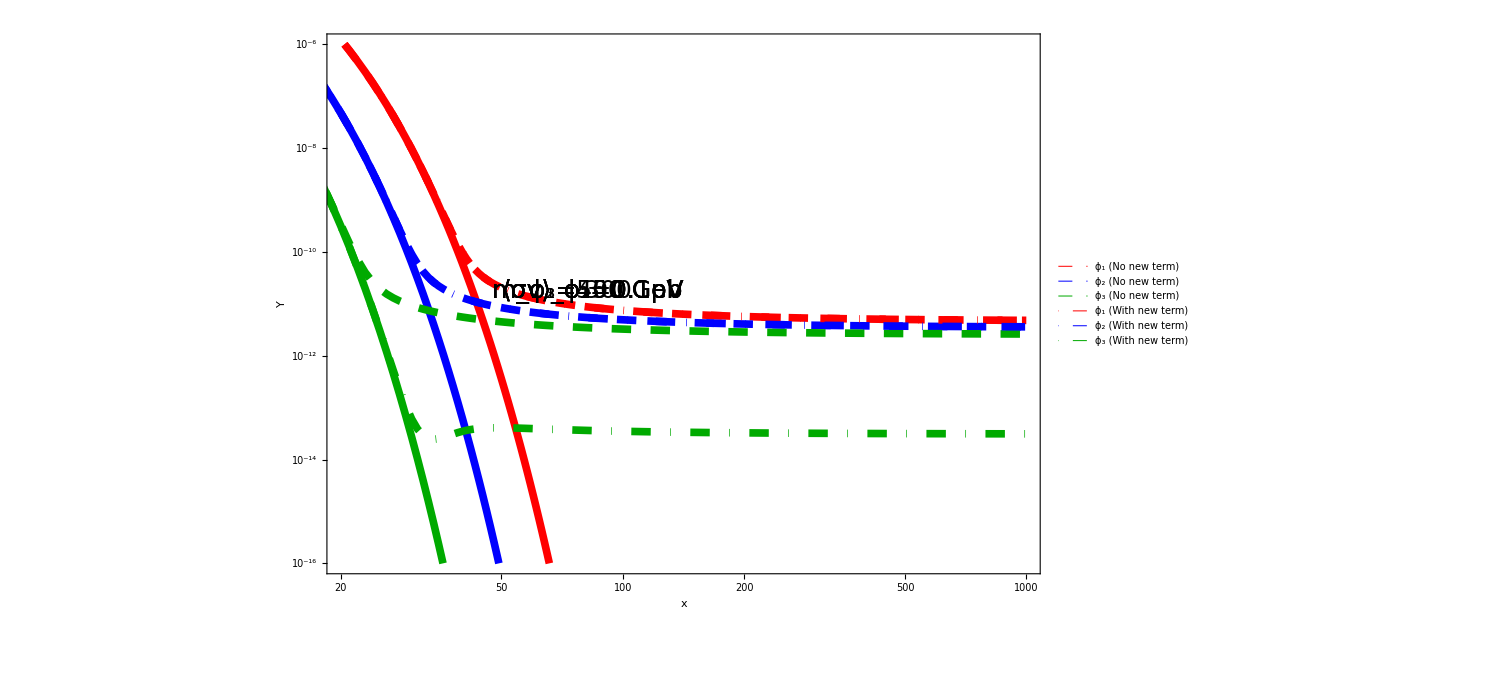

Axes::axes: {3.01529, {Thickness[Large]}} is not a valid axis specification.

Axes::axes: {-36.7262, {Thickness[Large]}} is not a valid axis specification.

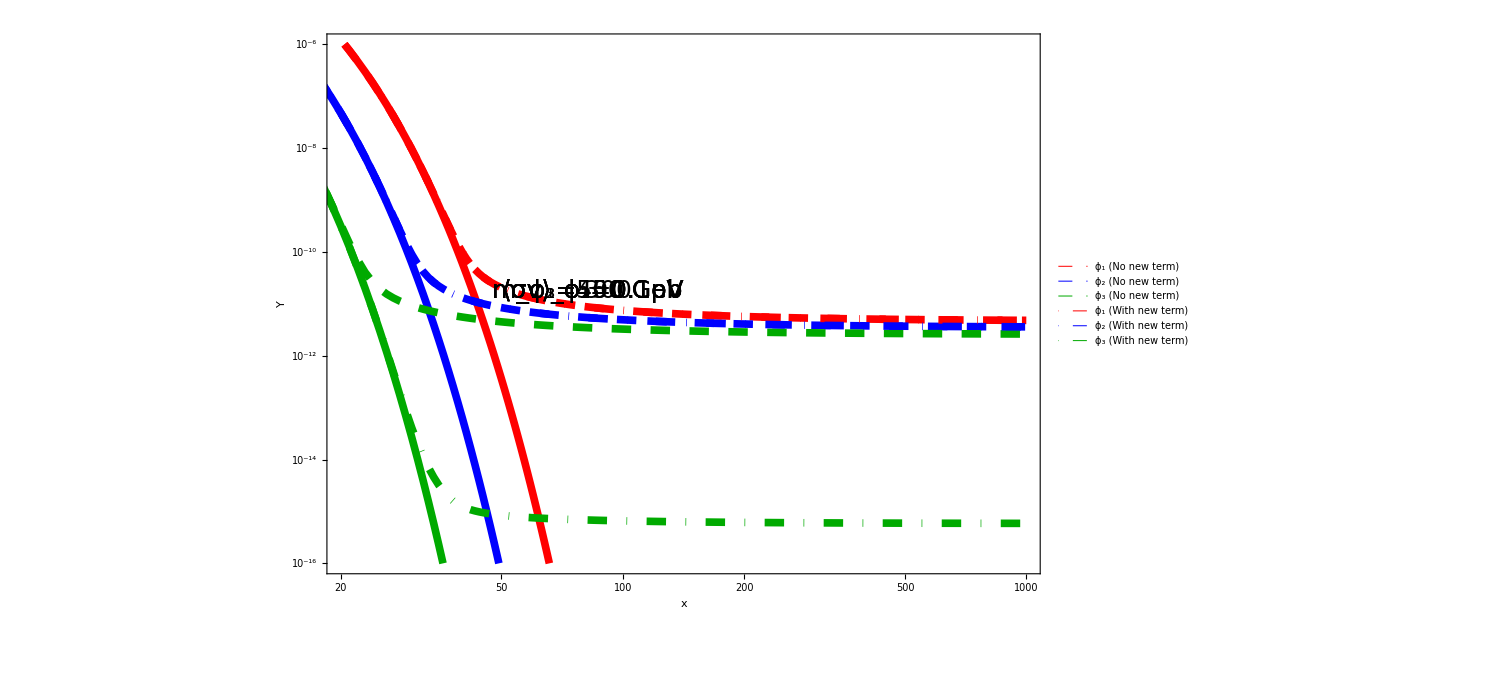

```mathematica
file= Import["C:\\Users\\AlexandrePoulin\\Documents\\relic\\freezeout_v2.5\\outputFiles\\waveTest\\outputOmegaBase3Diff.txt","Data"];
file2= Import["C:\\Users\\AlexandrePoulin\\Documents\\relic\\freezeout_v2.5\\outputFiles\\waveTest\\outputOmegaOneWay.txt","Data"];
file3= Import["C:\\Users\\AlexandrePoulin\\Documents\\relic\\freezeout_v2.5\\outputFiles\\waveTest\\outputOmegaOneWay2.txt","Data"];


numDM = 3;

thick=Thickness[0.005];
dashed=Dashing[Large];
dotdash=Dashing[{0,Large,Large,Large}];
plotStyle = {{Red,thick},{Blue,thick},{Darker[Green],thick},{Red,thick,dashed},{Blue,thick,dashed},{Darker[Green],thick,dashed}};
plotStyle2 = {{Red,thick,dotdash},{Blue,thick,dotdash},{Darker[Green],thick,dotdash}};
plotStyle3 = {{Blue,thick,dotdash},{Red,thick,dotdash},{Darker[Green],thick,dotdash}};

massScale=550;
(*should get 0.110 and 0.0128 for omegas *)

plotDataeq = Table[Table[{massScale/file[[a]][[1]],file[[a]][[2*b]]},{a,Length[file]}],{b,1,numDM}];
plotData= Table[Table[{massScale/file[[a]][[1]],file[[a]][[2*b+1]]},{a,Length[file]}],{b,1,numDM}];

plotDataeq2 = Table[Table[{massScale/file2[[a]][[1]],file2[[a]][[2*b]]},{a,Length[file2]}],{b,1,numDM}];
plotData2= Table[Table[{massScale/file2[[a]][[1]],file2[[a]][[2*b+1]]},{a,Length[file2]}],{b,1,numDM}];

plotDataeq3 = Table[Table[{massScale/file3[[a]][[1]],file3[[a]][[2*b]]},{a,Length[file3]}],{b,1,numDM}];
plotData3= Table[Table[{massScale/file3[[a]][[1]],file3[[a]][[2*b+1]]},{a,Length[file3]}],{b,1,numDM}];




plot1=ListLogLogPlot[Join[plotDataeq,plotData],PlotRange->{{20,1000},{10^(-16),10^-6}},Joined->True,PlotStyle->plotStyle(*,PlotLegends->{"Y_eq","Y"}*),BaseStyle->{FontSize->20},ImageSize->{1100,750},AxesStyle->Thick,PlotLegends->Placed[LineLegend[{{Red,dashed,Thickness[0.01]},{Blue,dashed,Thickness[0.01]},{Darker[Green],dashed,Thickness[0.01]},{Red,dotdash,Thickness[0.01]},{Blue,dotdash,Thickness[0.01]},{Darker[Green],dotdash,Thickness[0.01]},White},{"ϕ_1 (No new term)","ϕ_2 (No new term)","ϕ_3 (No new term)","ϕ_1 (With new term)","ϕ_2 (With new term)","ϕ_3 (With new term)"," "},LabelStyle->{25},LegendMarkerSize->{{100,20}}],{Right,Top}]];
plot2=ListLogLogPlot[plotData2,PlotRange->{{10,1000},{10^(-17),10^-7}},Joined->True,PlotStyle->plotStyle2(*,PlotLegends->{"Y_eq","Y"}*),BaseStyle->{FontSize->20},ImageSize->{1100,750},AxesStyle->Thick];
plot3=ListLogLogPlot[plotData3,PlotRange->{{10,1000},{10^(-20),10^-7}},Joined->True,PlotStyle->plotStyle2(*,PlotLegends->{"Y_eq","Y"}*),BaseStyle->{FontSize->20},ImageSize->{1100,750},AxesStyle->Thick];

Show[{plot1,plot2},FrameStyle->Thickness[0.005],FrameTicks->getTicks[plot1],BaseStyle->{FontSize->50},Frame-> True,FrameLabel->{"x"," Y"},LabelStyle->Black,Epilog->{Text[Style["m_ϕ_1= 300GeV",25,Black],Scaled[{0.5,0.5}],{0.5,-14}],
Text[Style["m_ϕ_2=400 GeV",25,Black],Scaled[{0.5,0.5}],{0.5,-12}],
Text[Style["m_ϕ_3=550 GeV",25,Black],Scaled[{0.5,0.5}],{0.5,-10}],
Text[Style["⟨σv⟩_ϕ_1=0.1pb",25,Black],Scaled[{0.5,0.5}],{0.5,-8}],
Text[Style["⟨σv⟩_ϕ_2=0.1pb",25,Black],Scaled[{0.5,0.5}],{0.5,-6}],
Text[Style["⟨σv⟩_ϕ_3=0.1pb",25,Black],Scaled[{0.5,0.5}],{0.5,-4}],
Text[Style["⟨σv⟩_ϕ_1=0.1pb",25,Black],Scaled[{0.5,0.5}],{0.5,-2}]}]
Show[{plot1,plot3},FrameStyle->Thickness[0.005],FrameTicks->getTicks[plot1],BaseStyle->{FontSize->50},Frame-> True,FrameLabel->{"x"," Y"},LabelStyle->Black,Epilog->{Text[Style["m_ϕ_1= 300GeV",25,Black],Scaled[{0.5,0.5}],{0.5,-14}],
Text[Style["m_ϕ_2=400 GeV",25,Black],Scaled[{0.5,0.5}],{0.5,-12}],
Text[Style["m_ϕ_3=550 GeV",25,Black],Scaled[{0.5,0.5}],{0.5,-10}],
Text[Style["⟨σv⟩_ϕ_1=0.1pb",25,Black],Scaled[{0.5,0.5}],{0.5,-8}],
Text[Style["⟨σv⟩_ϕ_2=0.1pb",25,Black],Scaled[{0.5,0.5}],{0.5,-6}],
Text[Style["⟨σv⟩_ϕ_3=0.1pb",25,Black],Scaled[{0.5,0.5}],{0.5,-4}],
Text[Style["⟨σv⟩_ϕ_1=0.1pb",25,Black],Scaled[{0.5,0.5}],{0.5,-2}]}]
```

```mathematica
LineLegend[{{Red,dashed},{Blue,dashed},{Red,dotdash},{Blue,dotdash},White},{Style["ϕ_1",25],Style["ϕ_2",25],Style["ϕ_1 (interaction)",25],Style["ϕ_2 (interaction)",25]," "},LegendMarkerSize->40]
```

```mathematica
LineLegend[{{Red,dashed},{Blue,dashed},White},{"red","green"," "},LegendMarkerSize->100]
```

```mathematica
dotdash
```

Dashing[{0,Large,Large,Large}]